```mathematica
Table[ShowGraph5Least[k],{k,allGraphs5TreeKeys}]
```

{-Graphics-590481,-Graphics-582881,-Graphics-552522,-Graphics-567701,-Graphics-560121,-Graphics-461803,-Graphics-461842,-Graphics-476942,-Graphics-469421,-Graphics-507181,-Graphics-522321,-Graphics-514780,-Graphics-484602,-Graphics-499721,-Graphics-492201,-Graphics-199365,-Graphics-199403,-Graphics-199692,-Graphics-200293,-Graphics-200602,-Graphics-214203,-Graphics-215102,-Graphics-207212,-Graphics-208121,-Graphics-243842,-Graphics-244141,-Graphics-258682,-Graphics-251680,-Graphics-222871,-Graphics-223180,-Graphics-237701,-Graphics-230721,-Graphics-331301,-Graphics-331581,-Graphics-346201,-Graphics-339160,-Graphics-375481,-Graphics-390141,-Graphics-383080,-Graphics-354340,-Graphics-368980,-Graphics-361940,-Graphics-268213,-Graphics-268522,-Graphics-283082,-Graphics-276101,-Graphics-312241,-Graphics-326841,-Graphics-319840,-Graphics-291282,-Graphics-305861,-Graphics-298881}

```mathematica
Table[GraphComplement[allGraphs5[k,"graph"]],{k,allGraphs5TreeKeys}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[IntegerDigits[K5Key,3]]
```

10

```mathematica
Convert[n_]:=FromDigits[Map[If[#==0,1,If[#==1,0,#]]&,PadLeft[IntegerDigits[n,3],10,0]],3]
```

```mathematica
IntegerDigits[33130,3]
```

{1,2,0,0,1,1,0,0,0,1}

```mathematica
Convert[33130]
```

16077

```mathematica
Table[ShowGraph5Least[Convert[k]],{k,allGraphs5TreeKeys}]
```

{-Graphics-590481,-Graphics-575282,-Graphics-537333,-Graphics-544922,-Graphics-529762,-Graphics-423934,-Graphics-423923,-Graphics-431473,-Graphics-416402,-Graphics-446592,-Graphics-454162,-Graphics-439081,-Graphics-401403,-Graphics-408962,-Graphics-393922,-Graphics-95883,-Graphics-95874,-Graphics-95642,-Graphics-95224,-Graphics-95033,-Graphics-102914,-Graphics-102283,-Graphics-88842,-Graphics-88202,-Graphics-117011,-Graphics-116800,-Graphics-124073,-Graphics-109981,-Graphics-74802,-Graphics-74581,-Graphics-81842,-Graphics-67792,-Graphics-160772,-Graphics-160522,-Graphics-167832,-Graphics-153721,-Graphics-182472,-Graphics-189802,-Graphics-175681,-Graphics-140161,-Graphics-147481,-Graphics-133401,-Graphics-34324,-Graphics-34043,-Graphics-41323,-Graphics-27332,-Graphics-55902,-Graphics-63202,-Graphics-49201,-Graphics-13953,-Graphics-21242,-Graphics-7282}

```mathematica
Table[ShowGraph5Least[Convert[k]],{k,allGraphs5TreeKeys}]
```

{-Graphics-590481,-Graphics-575282,-Graphics-537333,-Graphics-544922,-Graphics-529762,-Graphics-423934,-Graphics-423923,-Graphics-431473,-Graphics-416402,-Graphics-446592,-Graphics-454162,-Graphics-439081,-Graphics-401403,-Graphics-408962,-Graphics-393922,-Graphics-95883,-Graphics-95874,-Graphics-95642,-Graphics-95224,-Graphics-95033,-Graphics-102914,-Graphics-102283,-Graphics-88842,-Graphics-88202,-Graphics-117011,-Graphics-116800,-Graphics-124073,-Graphics-109981,-Graphics-74802,-Graphics-74581,-Graphics-81842,-Graphics-67792,-Graphics-160772,-Graphics-160522,-Graphics-167832,-Graphics-153721,-Graphics-182472,-Graphics-189802,-Graphics-175681,-Graphics-140161,-Graphics-147481,-Graphics-133401,-Graphics-34324,-Graphics-34043,-Graphics-41323,-Graphics-27332,-Graphics-55902,-Graphics-63202,-Graphics-49201,-Graphics-13953,-Graphics-21242,-Graphics-7282}

```mathematica
Table[SetsToSymbol[allGraphs5[Convert[k],"vertexsets"],"u"],{k,allGraphs5TreeKeys}]
```

{u12345,u1234x5,u123x4x5,u1235x4,u123x45,u12x3x4x5,u12x3x45,u125x3x4,u12x35x4,u124x3x5,u1245x3,u124x35,u12x34x5,u125x34,u12x345,u1x2x3x4x5,u1x2x3x45,u1x2x35x4,u1x2x34x5,u1x2x345,u15x2x3x4,u15x2x34,u1x25x3x4,u1x25x34,u14x2x3x5,u14x2x35,u145x2x3,u14x25x3,u1x24x3x5,u1x24x35,u15x24x3,u1x245x3,u13x2x4x5,u13x2x45,u135x2x4,u13x25x4,u134x2x5,u1345x2,u134x25,u13x24x5,u135x24,u13x245,u1x23x4x5,u1x23x45,u15x23x4,u1x235x4,u14x23x5,u145x23,u14x235,u1x234x5,u15x234,u1x2345}

```mathematica
Clear[u12345,u1234x5,u123x4x5,u1235x4,u123x45,u12x3x4x5,u12x3x45,u125x3x4,u12x35x4,u124x3x5,u1245x3,u124x35,u12x34x5,u125x34,u12x345,u1x2x3x4x5,u1x2x3x45,u1x2x35x4,u1x2x34x5,u1x2x345,u15x2x3x4,u15x2x34,u1x25x3x4,u1x25x34,u14x2x3x5,u14x2x35,u145x2x3,u14x25x3,u1x24x3x5,u1x24x35,u15x24x3,u1x245x3,u13x2x4x5,u13x2x45,u135x2x4,u13x25x4,u134x2x5,u1345x2,u134x25,u13x24x5,u135x24,u13x245,u1x23x4x5,u1x23x45,u15x23x4,u1x235x4,u14x23x5,u145x23,u14x235,u1x234x5,u15x234,u1x2345]
```

```mathematica
Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x35x4,v1x2x34x5,v1x2x345,v1x25x3x4,v1x25x34,v1x24x3x5,v1x24x35,v1x245x3,v1x23x4x5,v1x23x45,v1x235x4,v1x234x5,v1x2345,v15x2x3x4,v15x2x34,v15x24x3,v15x23x4,v15x234,v14x2x3x5,v14x2x35,v14x25x3,v14x23x5,v14x235,v145x2x3,v145x23,v13x2x4x5,v13x2x45,v13x25x4,v13x24x5,v13x245,v135x2x4,v135x24,v134x2x5,v134x25,v1345x2,v12x3x4x5,v12x3x45,v12x35x4,v12x34x5,v12x345,v125x3x4,v125x34,v124x3x5,v124x35,v1245x3,v123x4x5,v123x45,v1235x4,v1234x5,v12345}

```mathematica
rep=First[Solve[Fold[And,Table[SetsToSymbol[allGraphs5[Convert[k],"vertexsets"],"u"]==allGraphs5[Convert[k],"colofour"],{k,allGraphs5TreeKeys}]],Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]]];
```

```mathematica
Length[rep]
```

52

```mathematica
Table[allGraphs5[k,"colotree2"]=(allGraphs5[k,"colofour"]/.rep),{k,allGraphs5AtomKeys}]
```

{14 u12345-5 u1234x5-2 u123x45+2 u123x4x5-2 u12x345+u12x34x5+u12x3x45-u12x3x4x5-5 u1x2345+2 u1x234x5+u1x23x45-u1x23x4x5+2 u1x2x345-u1x2x34x5-u1x2x3x45+u1x2x3x4x5,-5 u12345+2 u123x45+u12x345-u12x3x45+2 u1x2345-u1x23x45-u1x2x345+u1x2x3x45,-5 u12345+2 u1235x4+u12x345-u12x35x4+2 u1x2345-u1x235x4-u1x2x345+u1x2x35x4,-5 u12345+2 u1234x5+u12x345-u12x34x5+2 u1x2345-u1x234x5-u1x2x345+u1x2x34x5,2 u12345-u12x345-u1x2345+u1x2x345,-5 u12345+2 u1235x4+u125x34-u125x3x4+2 u1x2345-u1x235x4-u1x25x34+u1x25x3x4,2 u12345-u125x34-u1x2345+u1x25x34,-5 u12345+2 u1234x5+u124x35-u124x3x5+2 u1x2345-u1x234x5-u1x24x35+u1x24x3x5,2 u12345-u124x35-u1x2345+u1x24x35,2 u12345-u1245x3-u1x2345+u1x245x3,-5 u12345+2 u1234x5+u123x45-u123x4x5+2 u1x2345-u1x234x5-u1x23x45+u1x23x4x5,2 u12345-u123x45-u1x2345+u1x23x45,2 u12345-u1235x4-u1x2345+u1x235x4,2 u12345-u1234x5-u1x2345+u1x234x5,-u12345+u1x2345,-5 u12345+2 u1235x4+u125x34-u125x3x4+2 u15x234-u15x23x4-u15x2x34+u15x2x3x4,2 u12345-u125x34-u15x234+u15x2x34,2 u12345-u1245x3-u15x234+u15x24x3,2 u12345-u1235x4-u15x234+u15x23x4,-u12345+u15x234,-5 u12345+2 u1234x5+u124x35-u124x3x5+2 u14x235-u14x23x5-u14x2x35+u14x2x3x5,2 u12345-u124x35-u14x235+u14x2x35,2 u12345-u1245x3-u14x235+u14x25x3,2 u12345-u1234x5-u14x235+u14x23x5,-u12345+u14x235,2 u12345-u1245x3-u145x23+u145x2x3,-u12345+u145x23,-5 u12345+2 u1234x5+u123x45-u123x4x5+2 u13x245-u13x24x5-u13x2x45+u13x2x4x5,2 u12345-u123x45-u13x245+u13x2x45,2 u12345-u1235x4-u13x245+u13x25x4,2 u12345-u1234x5-u13x245+u13x24x5,-u12345+u13x245,2 u12345-u1235x4-u135x24+u135x2x4,-u12345+u135x24,2 u12345-u1234x5-u134x25+u134x2x5,-u12345+u134x25,-u12345+u1345x2,-5 u12345+2 u1234x5+u123x45-u123x4x5+2 u12x345-u12x34x5-u12x3x45+u12x3x4x5,2 u12345-u123x45-u12x345+u12x3x45,2 u12345-u1235x4-u12x345+u12x35x4,2 u12345-u1234x5-u12x345+u12x34x5,-u12345+u12x345,2 u12345-u1235x4-u125x34+u125x3x4,-u12345+u125x34,2 u12345-u1234x5-u124x35+u124x3x5,-u12345+u124x35,-u12345+u1245x3,2 u12345-u1234x5-u123x45+u123x4x5,-u12345+u123x45,-u12345+u1235x4,-u12345+u1234x5,u12345}

```mathematica
Table[allGraphs5[k,"colotree2"],{k,allGraphs5AtomKeys}]
```

{14 u12345-5 u1234x5-2 u123x45+2 u123x4x5-2 u12x345+u12x34x5+u12x3x45-u12x3x4x5-5 u1x2345+2 u1x234x5+u1x23x45-u1x23x4x5+2 u1x2x345-u1x2x34x5-u1x2x3x45+u1x2x3x4x5,-5 u12345+2 u123x45+u12x345-u12x3x45+2 u1x2345-u1x23x45-u1x2x345+u1x2x3x45,-5 u12345+2 u1235x4+u12x345-u12x35x4+2 u1x2345-u1x235x4-u1x2x345+u1x2x35x4,-5 u12345+2 u1234x5+u12x345-u12x34x5+2 u1x2345-u1x234x5-u1x2x345+u1x2x34x5,2 u12345-u12x345-u1x2345+u1x2x345,-5 u12345+2 u1235x4+u125x34-u125x3x4+2 u1x2345-u1x235x4-u1x25x34+u1x25x3x4,2 u12345-u125x34-u1x2345+u1x25x34,-5 u12345+2 u1234x5+u124x35-u124x3x5+2 u1x2345-u1x234x5-u1x24x35+u1x24x3x5,2 u12345-u124x35-u1x2345+u1x24x35,2 u12345-u1245x3-u1x2345+u1x245x3,-5 u12345+2 u1234x5+u123x45-u123x4x5+2 u1x2345-u1x234x5-u1x23x45+u1x23x4x5,2 u12345-u123x45-u1x2345+u1x23x45,2 u12345-u1235x4-u1x2345+u1x235x4,2 u12345-u1234x5-u1x2345+u1x234x5,-u12345+u1x2345,-5 u12345+2 u1235x4+u125x34-u125x3x4+2 u15x234-u15x23x4-u15x2x34+u15x2x3x4,2 u12345-u125x34-u15x234+u15x2x34,2 u12345-u1245x3-u15x234+u15x24x3,2 u12345-u1235x4-u15x234+u15x23x4,-u12345+u15x234,-5 u12345+2 u1234x5+u124x35-u124x3x5+2 u14x235-u14x23x5-u14x2x35+u14x2x3x5,2 u12345-u124x35-u14x235+u14x2x35,2 u12345-u1245x3-u14x235+u14x25x3,2 u12345-u1234x5-u14x235+u14x23x5,-u12345+u14x235,2 u12345-u1245x3-u145x23+u145x2x3,-u12345+u145x23,-5 u12345+2 u1234x5+u123x45-u123x4x5+2 u13x245-u13x24x5-u13x2x45+u13x2x4x5,2 u12345-u123x45-u13x245+u13x2x45,2 u12345-u1235x4-u13x245+u13x25x4,2 u12345-u1234x5-u13x245+u13x24x5,-u12345+u13x245,2 u12345-u1235x4-u135x24+u135x2x4,-u12345+u135x24,2 u12345-u1234x5-u134x25+u134x2x5,-u12345+u134x25,-u12345+u1345x2,-5 u12345+2 u1234x5+u123x45-u123x4x5+2 u12x345-u12x34x5-u12x3x45+u12x3x4x5,2 u12345-u123x45-u12x345+u12x3x45,2 u12345-u1235x4-u12x345+u12x35x4,2 u12345-u1234x5-u12x345+u12x34x5,-u12345+u12x345,2 u12345-u1235x4-u125x34+u125x3x4,-u12345+u125x34,2 u12345-u1234x5-u124x35+u124x3x5,-u12345+u124x35,-u12345+u1245x3,2 u12345-u1234x5-u123x45+u123x4x5,-u12345+u123x45,-u12345+u1235x4,-u12345+u1234x5,u12345}

```mathematica
Monitor[Table[allGraphs5[k,"colotree2"]=Simplify[(allGraphs5[k,"colofour"]/.rep)],{k,Keys[allGraphs5]}],k]
```

{u1234x5+u1235x4-3 u1245x3-u124x3x5-u125x3x4+u1345x2+u134x2x5+u135x2x4+u13x25x4+u13x2x4x5+u145x2x3+u14x25x3+u14x2x3x5+u15x24x3+u15x2x3x4+u1x2345-u1x235x4+u1x245x3+u1x24x3x5+u1x25x3x4+u1x2x35x4+u1x2x3x4x5,-u12345+u1234x5+2 u1235x4-4 u1245x3-2 u124x3x5-2 u125x3x4-u12x35x4-u12x3x4x5+u1345x2+u134x2x5+u135x2x4+u13x25x4+u13x2x4x5+u145x2x3+u14x25x3+u14x2x3x5+u15x24x3+u15x2x3x4+u1x2345-u1x235x4+u1x245x3+u1x24x3x5+u1x25x3x4+u1x2x35x4+u1x2x3x4x5,1892,u12345-u1245x3+u1345x2+u13x2x45+u145x2x3+u1x245x3+u1x2x3x45}
 |  |  |  |

```mathematica
Bases=Block[{result},
result=Association[];
result["C"]=Association[];
result["C","Colofour"]="colofour";
result["E"]=Association[];
result["E","Colofour"]="colofourrealnull";
result["G"]=Association[];
result["G","Colofour"]="colofourgenerator";
result["F"]=Association[];
result["F","Colofour"]="colofournull";
result["T"]=Association[];
result["T","Colofour"]="colotree";
result["Z"]=Association[];
result["Z","Colofour"]="colotree2";
Table[result[base,"AtomKeys"]=Sort[Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,result[base,"Colofour"]]]]==1&],MyComp[allGraphs5[#1,result[base,"Colofour"]],allGraphs5[#2,result[base,"Colofour"]]]&]
,{base,Keys[result]}];
Table[result[base,"Variables"]=Table[allGraphs5[k,result[base,"Colofour"]],{k,result[base,"AtomKeys"]}]
,{base,Keys[result]}];
result
]
```

<|C→<|Colofour→colofour,AtomKeys→{29524,49207,36085,31711,30253,29767,29605,29551,29533,29527,29525,56011,51475,49963,49216,49210,49208,38281,36817,36166,36112,36086,32441,31954,31738,31714,30496,30334,30262,29857,29797,29768,29633,29608,29560,29537,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{v1x2x3x4x5,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v123x4x5,v124x3x5,v125x3x4,v12x34x5,v12x35x4,v12x3x45,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v145x2x3,v14x23x5,v14x25x3,v14x2x35,v15x23x4,v15x24x3,v15x2x34,v1x234x5,v1x235x4,v1x23x45,v1x245x3,v1x24x35,v1x25x34,v1x2x345,v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345,v12345}|>,E→<|Colofour→colofourrealnull,AtomKeys→{0,39366,13122,4374,1458,486,162,54,18,6,2,52974,43902,40878,39384,39372,39368,17514,14586,13284,13176,13124,5834,4860,4428,4380,1944,1620,1476,666,546,488,218,168,72,26,57528,54492,52976,45416,43908,40896,39392,18980,17568,14748,13340,6320,4920,2124,728,59048},Variables→{n1x2x3x4x5,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n1x2x34x5,n1x2x35x4,n1x2x3x45,n123x4x5,n124x3x5,n125x3x4,n12x34x5,n12x35x4,n12x3x45,n134x2x5,n135x2x4,n13x24x5,n13x25x4,n13x2x45,n145x2x3,n14x23x5,n14x25x3,n14x2x35,n15x23x4,n15x24x3,n15x2x34,n1x234x5,n1x235x4,n1x23x45,n1x245x3,n1x24x35,n1x25x34,n1x2x345,n1234x5,n1235x4,n123x45,n1245x3,n124x35,n125x34,n12x345,n1345x2,n134x25,n135x24,n13x245,n145x23,n14x235,n15x234,n1x2345,n12345}|>,G→<|Colofour→colofourgenerator,AtomKeys→{29524,9841,22963,27337,28795,29281,29443,29497,29515,29521,29523,3037,7573,9085,9832,9838,9840,20767,22231,22882,22936,22962,26607,27094,27310,27334,28552,28714,28786,29191,29251,29280,29415,29440,29488,29511,760,2278,3036,6816,7570,9076,9828,20034,20740,22150,22854,26364,27064,28462,29160,0},Variables→{g1x2x3x4x5,g12x3x4x5,g13x2x4x5,g14x2x3x5,g15x2x3x4,g1x23x4x5,g1x24x3x5,g1x25x3x4,g1x2x34x5,g1x2x35x4,g1x2x3x45,g123x4x5,g124x3x5,g125x3x4,g12x34x5,g12x35x4,g12x3x45,g134x2x5,g135x2x4,g13x24x5,g13x25x4,g13x2x45,g145x2x3,g14x23x5,g14x25x3,g14x2x35,g15x23x4,g15x24x3,g15x2x34,g1x234x5,g1x235x4,g1x23x45,g1x245x3,g1x24x35,g1x25x34,g1x2x345,g1234x5,g1235x4,g123x45,g1245x3,g124x35,g125x34,g12x345,g1345x2,g134x25,g135x24,g13x245,g145x23,g14x235,g15x234,g1x2345,g12345}|>,F→<|Colofour→colofournull,AtomKeys→{0,19683,6561,2187,729,243,81,27,9,3,1,26487,21951,20439,19692,19686,19684,8757,7293,6642,6588,6562,2917,2430,2214,2190,972,810,738,333,273,244,109,84,36,13,28764,27246,26488,22708,21954,20448,19696,9490,8784,7374,6670,3160,2460,1062,364,29524},Variables→{p1x2x3x4x5,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p1x2x34x5,p1x2x35x4,p1x2x3x45,p123x4x5,p124x3x5,p125x3x4,p12x34x5,p12x35x4,p12x3x45,p134x2x5,p135x2x4,p13x24x5,p13x25x4,p13x2x45,p145x2x3,p14x23x5,p14x25x3,p14x2x35,p15x23x4,p15x24x3,p15x2x34,p1x234x5,p1x235x4,p1x23x45,p1x245x3,p1x24x35,p1x25x34,p1x2x345,p1234x5,p1235x4,p123x45,p1245x3,p124x35,p125x34,p12x345,p1345x2,p134x25,p135x24,p13x245,p145x23,p14x235,p15x234,p1x2345,p12345}|>,T→<|Colofour→colotree,AtomKeys→{19936,46180,33130,24384,21420,26821,22287,20721,20029,19969,19940,55252,50718,47694,48460,46942,46184,37548,34620,35434,33916,33158,25868,31224,25168,24414,28308,23770,21510,29128,27610,26852,23072,22318,20812,20060,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{t1x2x3x4x5,t12x3x4x5,t13x2x4x5,t14x2x3x5,t15x2x3x4,t1x23x4x5,t1x24x3x5,t1x25x3x4,t1x2x34x5,t1x2x35x4,t1x2x3x45,t123x4x5,t124x3x5,t125x3x4,t12x34x5,t12x35x4,t12x3x45,t134x2x5,t135x2x4,t13x24x5,t13x25x4,t13x2x45,t145x2x3,t14x23x5,t14x25x3,t14x2x35,t15x23x4,t15x24x3,t15x2x34,t1x234x5,t1x235x4,t1x23x45,t1x245x3,t1x24x35,t1x25x34,t1x2x345,t1234x5,t1235x4,t123x45,t1245x3,t124x35,t125x34,t12x345,t1345x2,t134x25,t135x24,t13x245,t145x23,t14x235,t15x234,t1x2345,t12345}|>,Z→<|Colofour→colotree2,AtomKeys→{9588,42393,16077,11701,10291,3432,7480,8884,9522,9564,9587,53733,44659,43147,40140,41640,42392,18247,16783,14016,15372,16052,12407,5590,10998,11680,4132,8184,10228,1395,2733,3404,6779,7458,8820,9503,57528,54492,52976,45416,43908,40896,39392,18980,17568,14748,13340,6320,4920,2124,728,59048},Variables→{u1x2x3x4x5,u12x3x4x5,u13x2x4x5,u14x2x3x5,u15x2x3x4,u1x23x4x5,u1x24x3x5,u1x25x3x4,u1x2x34x5,u1x2x35x4,u1x2x3x45,u123x4x5,u124x3x5,u125x3x4,u12x34x5,u12x35x4,u12x3x45,u134x2x5,u135x2x4,u13x24x5,u13x25x4,u13x2x45,u145x2x3,u14x23x5,u14x25x3,u14x2x35,u15x23x4,u15x24x3,u15x2x34,u1x234x5,u1x235x4,u1x23x45,u1x245x3,u1x24x35,u1x25x34,u1x2x345,u1234x5,u1235x4,u123x45,u1245x3,u124x35,u125x34,u12x345,u1345x2,u134x25,u135x24,u13x245,u145x23,u14x235,u15x234,u1x2345,u12345}|>|>

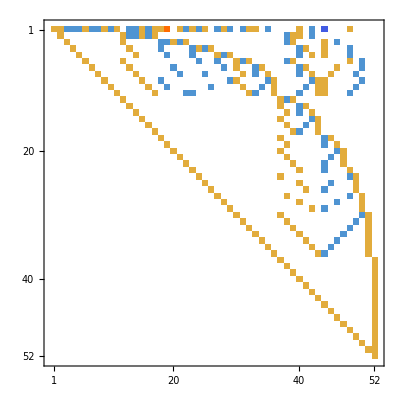
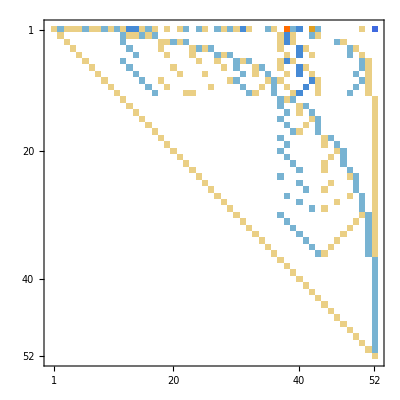

```mathematica
{a,b}={ConversionMatrix["Z","T"],ConversionMatrix["T","Z"]};Map[MatrixPlot,{a,b}]
```

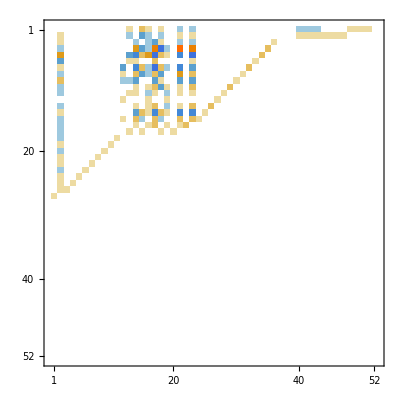

```mathematica
Eigenvectors[a]//MatrixPlot
```

```mathematica
Eigenvectors[b]//MatrixPlot
```

-Graphics-

```mathematica
a==b
```

True

```mathematica
ConversionMatrix["T","Z"]//MatrixPlot
```

-Graphics-

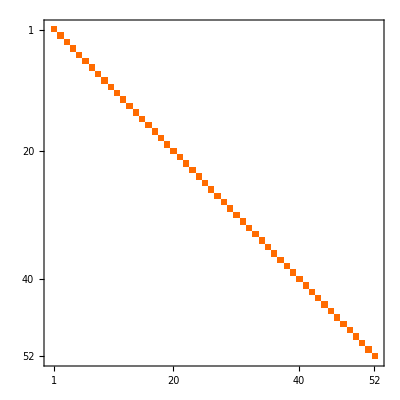
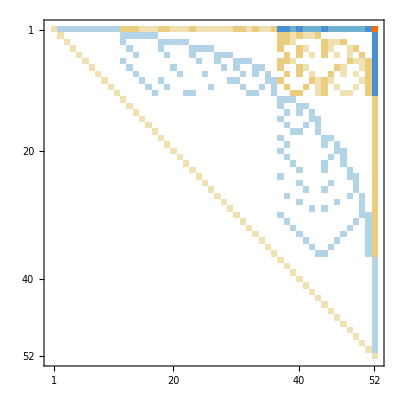
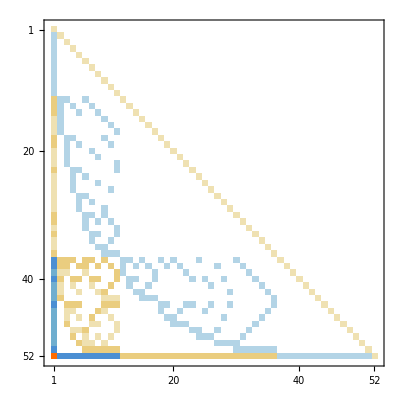
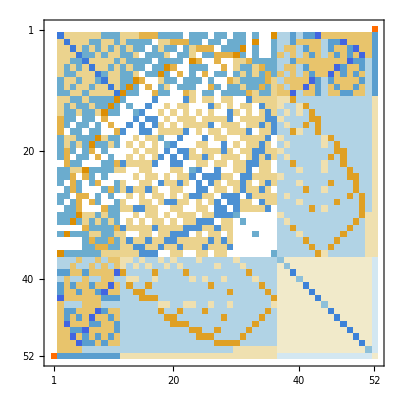
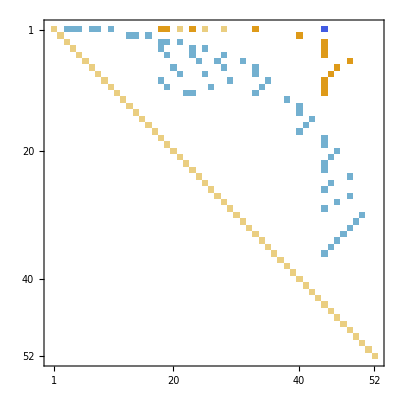
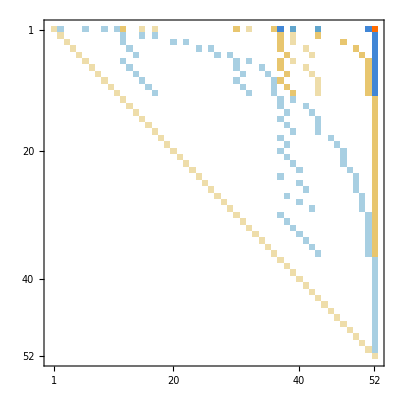
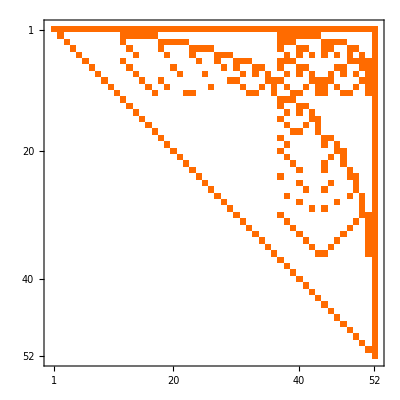
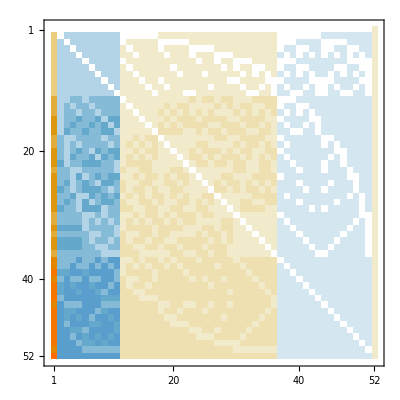
{{-Graphics-C→C,-Graphics-C→E,-Graphics-C→G,-Graphics-C→F,-Graphics-C→T,-Graphics-C→Z},{-Graphics-E→C,-Graphics-E→E,-Graphics-E→G,-Graphics-E→F,-Graphics-E→T,-Graphics-E→Z},{-Graphics-G→C,-Graphics-G→E,-Graphics-G→G,-Graphics-G→F,-Graphics-G→T,-Graphics-G→Z},{-Graphics-F→C,-Graphics-F→E,-Graphics-F→G,-Graphics-F→F,-Graphics-F→T,-Graphics-F→Z},{-Graphics-T→C,-Graphics-T→E,-Graphics-T→G,-Graphics-T→F,-Graphics-T→T,-Graphics-T→Z},{-Graphics-Z→C,-Graphics-Z→E,-Graphics-Z→G,-Graphics-Z→F,-Graphics-Z→T,-Graphics-Z→Z}}

```mathematica
Table[Labeled[MatrixPlot[ConversionMatrix[base1,base2]],base1->base2],{base1,Keys[Bases]},{base2,Keys[Bases]}]
```

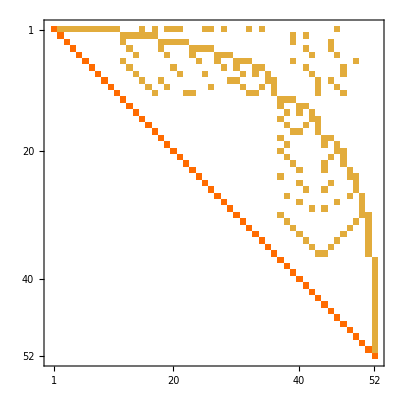

```mathematica
MatrixPlot[ConversionMatrix["Z","C"]+ConversionMatrix["T","C"]]
```

## En dan

```mathematica
Table[With[{g=allGraphs5[k,"graph"]},If[Mod[VertexCount[g],2]==1,ShowGraph5Least[Convert[k]],ShowGraph5Least[k]]],{k,allGraphs5AtomKeys}]
```

{-Graphics-034,-Graphics-295250,-Graphics-295270,-Graphics-295330,-Graphics-265,-Graphics-295510,-Graphics-724,-Graphics-296050,-Graphics-1682,-Graphics-2184,-Graphics-297670,-Graphics-4885,-Graphics-5464,-Graphics-6665,-Graphics-298881,-Graphics-302530,-Graphics-14765,-Graphics-16204,-Graphics-19445,-Graphics-305861,-Graphics-317110,-Graphics-43802,-Graphics-44282,-Graphics-48604,-Graphics-319840,-Graphics-58345,-Graphics-326841,-Graphics-360850,-Graphics-131244,-Graphics-131762,-Graphics-132842,-Graphics-361940,-Graphics-145864,-Graphics-368980,-Graphics-175144,-Graphics-383080,-Graphics-390141,-Graphics-492070,-Graphics-393685,-Graphics-393724,-Graphics-393845,-Graphics-492201,-Graphics-408785,-Graphics-499721,-Graphics-439024,-Graphics-514780,-Graphics-522321,-Graphics-529745,-Graphics-560121,-Graphics-567701,-Graphics-582881,-Graphics-590481}

```mathematica
sets123=Table[With[{g=allGraphs5[k,"graph"]},If[Mod[VertexCount[g],2]==1,Convert[k],k]],{k,allGraphs5AtomKeys}]
```

{0,29525,29527,29533,26,29551,72,29605,168,218,29767,488,546,666,29888,30253,1476,1620,1944,30586,31711,4380,4428,4860,31984,5834,32684,36085,13124,13176,13284,36194,14586,36898,17514,38308,39014,49207,39368,39372,39384,49220,40878,49972,43902,51478,52232,52974,56012,56770,58288,59048}

```mathematica
Table[SetsToSymbol[allGraphs5[k,"vertexsets"],"z"],{k,sets123}]
```

{z1x2x3x4x5,z1x2x3x45,z1x2x35x4,z1x2x34x5,z1x2x345,z1x25x3x4,z1x25x34,z1x24x3x5,z1x24x35,z1x245x3,z1x23x4x5,z1x23x45,z1x235x4,z1x234x5,z1x2345,z15x2x3x4,z15x2x34,z15x24x3,z15x23x4,z15x234,z14x2x3x5,z14x2x35,z14x25x3,z14x23x5,z14x235,z145x2x3,z145x23,z13x2x4x5,z13x2x45,z13x25x4,z13x24x5,z13x245,z135x2x4,z135x24,z134x2x5,z134x25,z1345x2,z12x3x4x5,z12x3x45,z12x35x4,z12x34x5,z12x345,z125x3x4,z125x34,z124x3x5,z124x35,z1245x3,z123x4x5,z123x45,z1235x4,z1234x5,z12345}

```mathematica
rep123=First[Solve[Fold[And,Table[SetsToSymbol[allGraphs5[k,"vertexsets"],"z"]==allGraphs5[Convert[k],"colofour"],{k,sets123}]],Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]]];
```

```mathematica
rep123
```

{v1x2x3x4x5→z1x2x3x4x5,v1x2x3x45→6 z12345-z123x45-z1245x3-z12x345-z12x3x45-z1345x2-z13x245-z13x2x45-z145x23-z145x2x3-z1x2345-z1x23x45-z1x245x3-z1x2x345+z1x2x3x45,v1x2x35x4→6 z12345-z1235x4-z124x35-z12x345-z12x35x4-z1345x2-z135x24-z135x2x4-z14x235-z14x2x35-z1x2345-z1x235x4-z1x24x35-z1x2x345+z1x2x35x4,v1x2x34x5→6 z12345-z1234x5-z125x34-z12x345-z12x34x5-z1345x2-z134x25-z134x2x5-z15x234-z15x2x34-z1x2345-z1x234x5-z1x25x34-z1x2x345+z1x2x34x5,v1x2x345→z1x2x345,v1x25x3x4→6 z12345-z1235x4-z1245x3-z125x34-z125x3x4-z134x25-z13x245-z13x25x4-z14x235-z14x25x3-z1x2345-z1x235x4-z1x245x3-z1x25x34+z1x25x3x4,v1x25x34→z1x25x34,v1x24x3x5→6 z12345-z1234x5-z1245x3-z124x35-z124x3x5-z135x24-z13x245-z13x24x5-z15x234-z15x24x3-z1x2345-z1x234x5-z1x245x3-z1x24x35+z1x24x3x5,v1x24x35→z1x24x35,v1x245x3→z1x245x3,v1x23x4x5→6 z12345-z1234x5-z1235x4-z123x45-z123x4x5-z145x23-z14x235-z14x23x5-z15x234-z15x23x4-z1x2345-z1x234x5-z1x235x4-z1x23x45+z1x23x4x5,v1x23x45→z1x23x45,v1x235x4→z1x235x4,v1x234x5→z1x234x5,v1x2345→-z12345+z1x2345,v15x2x3x4→6 z12345-z1235x4-z1245x3-z125x34-z125x3x4-z1345x2-z135x24-z135x2x4-z145x23-z145x2x3-z15x234-z15x23x4-z15x24x3-z15x2x34+z15x2x3x4,v15x2x34→z15x2x34,v15x24x3→z15x24x3,v15x23x4→z15x23x4,v15x234→-z12345+z15x234,v14x2x3x5→6 z12345-z1234x5-z1245x3-z124x35-z124x3x5-z1345x2-z134x25-z134x2x5-z145x23-z145x2x3-z14x235-z14x23x5-z14x25x3-z14x2x35+z14x2x3x5,v14x2x35→z14x2x35,v14x25x3→z14x25x3,v14x23x5→z14x23x5,v14x235→-z12345+z14x235,v145x2x3→z145x2x3,v145x23→-z12345+z145x23,v13x2x4x5→6 z12345-z1234x5-z1235x4-z123x45-z123x4x5-z1345x2-z134x25-z134x2x5-z135x24-z135x2x4-z13x245-z13x24x5-z13x25x4-z13x2x45+z13x2x4x5,v13x2x45→z13x2x45,v13x25x4→z13x25x4,v13x24x5→z13x24x5,v13x245→-z12345+z13x245,v135x2x4→z135x2x4,v135x24→-z12345+z135x24,v134x2x5→z134x2x5,v134x25→-z12345+z134x25,v1345x2→-z12345+z1345x2,v12x3x4x5→6 z12345-z1234x5-z1235x4-z123x45-z123x4x5-z1245x3-z124x35-z124x3x5-z125x34-z125x3x4-z12x345-z12x34x5-z12x35x4-z12x3x45+z12x3x4x5,v12x3x45→z12x3x45,v12x35x4→z12x35x4,v12x34x5→z12x34x5,v12x345→-z12345+z12x345,v125x3x4→z125x3x4,v125x34→-z12345+z125x34,v124x3x5→z124x3x5,v124x35→-z12345+z124x35,v1245x3→-z12345+z1245x3,v123x4x5→z123x4x5,v123x45→-z12345+z123x45,v1235x4→-z12345+z1235x4,v1234x5→-z12345+z1234x5,v12345→z12345}

```mathematica
Monitor[Table[allGraphs5[k,"colotreejef"]=Simplify[(allGraphs5[k,"colofour"]/.rep123)],{k,Keys[allGraphs5]}],k]
```

{46 z12345-5 z1234x5-5 z1235x4-3 z123x45-2 z123x4x5-5 z1245x3-3 z124x35-2 z124x3x5-3 z125x34-2 z125x3x4-3 z12x345-z12x34x5-z12x35x4-z12x3x45+z12x3x4x5-5 z1345x2-3 z134x25-2 z134x2x5-3 z135x24-2 z135x2x4-3 z13x245-z13x24x5-z13x25x4-z13x2x45+z13x2x4x5-3 z145x23-2 z145x2x3-3 z14x235-z14x23x5-z14x25x3-z14x2x35+z14x2x3x5-3 z15x234-z15x23x4-z15x24x3-z15x2x34+z15x2x3x4-5 z1x2345-2 z1x234x5-2 z1x235x4-z1x23x45+z1x23x4x5-2 z1x245x3-z1x24x35+z1x24x3x5-z1x25x34+z1x25x3x4-2 z1x2x345+z1x2x34x5+z1x2x35x4+z1x2x3x45+z1x2x3x4x5,1893,z1x2x3x45}
 |  |  |  |

```mathematica
Bases=Block[{result},
result=Association[];
result["C"]=Association[];
result["C","Colofour"]="colofour";
result["E"]=Association[];
result["E","Colofour"]="colofourrealnull";
result["G"]=Association[];
result["G","Colofour"]="colofourgenerator";
result["F"]=Association[];
result["F","Colofour"]="colofournull";
result["T"]=Association[];
result["T","Colofour"]="colotree";
result["Z"]=Association[];
result["Z","Colofour"]="colotreejef";
Table[result[base,"AtomKeys"]=Sort[Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,result[base,"Colofour"]]]]==1&],MyComp[allGraphs5[#1,result[base,"Colofour"]],allGraphs5[#2,result[base,"Colofour"]]]&]
,{base,Keys[result]}];
Table[result[base,"Variables"]=Table[allGraphs5[k,result[base,"Colofour"]],{k,result[base,"AtomKeys"]}]
,{base,Keys[result]}];
result
]
```

<|C→<|Colofour→colofour,AtomKeys→{29524,49207,36085,31711,30253,29767,29605,29551,29533,29527,29525,56011,51475,49963,49216,49210,49208,38281,36817,36166,36112,36086,32441,31954,31738,31714,30496,30334,30262,29857,29797,29768,29633,29608,29560,29537,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{v1x2x3x4x5,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v123x4x5,v124x3x5,v125x3x4,v12x34x5,v12x35x4,v12x3x45,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v145x2x3,v14x23x5,v14x25x3,v14x2x35,v15x23x4,v15x24x3,v15x2x34,v1x234x5,v1x235x4,v1x23x45,v1x245x3,v1x24x35,v1x25x34,v1x2x345,v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345,v12345}|>,E→<|Colofour→colofourrealnull,AtomKeys→{0,39366,13122,4374,1458,486,162,54,18,6,2,52974,43902,40878,39384,39372,39368,17514,14586,13284,13176,13124,5834,4860,4428,4380,1944,1620,1476,666,546,488,218,168,72,26,57528,54492,52976,45416,43908,40896,39392,18980,17568,14748,13340,6320,4920,2124,728,59048},Variables→{n1x2x3x4x5,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n1x2x34x5,n1x2x35x4,n1x2x3x45,n123x4x5,n124x3x5,n125x3x4,n12x34x5,n12x35x4,n12x3x45,n134x2x5,n135x2x4,n13x24x5,n13x25x4,n13x2x45,n145x2x3,n14x23x5,n14x25x3,n14x2x35,n15x23x4,n15x24x3,n15x2x34,n1x234x5,n1x235x4,n1x23x45,n1x245x3,n1x24x35,n1x25x34,n1x2x345,n1234x5,n1235x4,n123x45,n1245x3,n124x35,n125x34,n12x345,n1345x2,n134x25,n135x24,n13x245,n145x23,n14x235,n15x234,n1x2345,n12345}|>,G→<|Colofour→colofourgenerator,AtomKeys→{29524,9841,22963,27337,28795,29281,29443,29497,29515,29521,29523,3037,7573,9085,9832,9838,9840,20767,22231,22882,22936,22962,26607,27094,27310,27334,28552,28714,28786,29191,29251,29280,29415,29440,29488,29511,760,2278,3036,6816,7570,9076,9828,20034,20740,22150,22854,26364,27064,28462,29160,0},Variables→{g1x2x3x4x5,g12x3x4x5,g13x2x4x5,g14x2x3x5,g15x2x3x4,g1x23x4x5,g1x24x3x5,g1x25x3x4,g1x2x34x5,g1x2x35x4,g1x2x3x45,g123x4x5,g124x3x5,g125x3x4,g12x34x5,g12x35x4,g12x3x45,g134x2x5,g135x2x4,g13x24x5,g13x25x4,g13x2x45,g145x2x3,g14x23x5,g14x25x3,g14x2x35,g15x23x4,g15x24x3,g15x2x34,g1x234x5,g1x235x4,g1x23x45,g1x245x3,g1x24x35,g1x25x34,g1x2x345,g1234x5,g1235x4,g123x45,g1245x3,g124x35,g125x34,g12x345,g1345x2,g134x25,g135x24,g13x245,g145x23,g14x235,g15x234,g1x2345,g12345}|>,F→<|Colofour→colofournull,AtomKeys→{0,19683,6561,2187,729,243,81,27,9,3,1,26487,21951,20439,19692,19686,19684,8757,7293,6642,6588,6562,2917,2430,2214,2190,972,810,738,333,273,244,109,84,36,13,28764,27246,26488,22708,21954,20448,19696,9490,8784,7374,6670,3160,2460,1062,364,29524},Variables→{p1x2x3x4x5,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p1x2x34x5,p1x2x35x4,p1x2x3x45,p123x4x5,p124x3x5,p125x3x4,p12x34x5,p12x35x4,p12x3x45,p134x2x5,p135x2x4,p13x24x5,p13x25x4,p13x2x45,p145x2x3,p14x23x5,p14x25x3,p14x2x35,p15x23x4,p15x24x3,p15x2x34,p1x234x5,p1x235x4,p1x23x45,p1x245x3,p1x24x35,p1x25x34,p1x2x345,p1234x5,p1235x4,p123x45,p1245x3,p124x35,p125x34,p12x345,p1345x2,p134x25,p135x24,p13x245,p145x23,p14x235,p15x234,p1x2345,p12345}|>,T→<|Colofour→colotree,AtomKeys→{19936,46180,33130,24384,21420,26821,22287,20721,20029,19969,19940,55252,50718,47694,48460,46942,46184,37548,34620,35434,33916,33158,25868,31224,25168,24414,28308,23770,21510,29128,27610,26852,23072,22318,20812,20060,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{t1x2x3x4x5,t12x3x4x5,t13x2x4x5,t14x2x3x5,t15x2x3x4,t1x23x4x5,t1x24x3x5,t1x25x3x4,t1x2x34x5,t1x2x35x4,t1x2x3x45,t123x4x5,t124x3x5,t125x3x4,t12x34x5,t12x35x4,t12x3x45,t134x2x5,t135x2x4,t13x24x5,t13x25x4,t13x2x45,t145x2x3,t14x23x5,t14x25x3,t14x2x35,t15x23x4,t15x24x3,t15x2x34,t1x234x5,t1x235x4,t1x23x45,t1x245x3,t1x24x35,t1x25x34,t1x2x345,t1234x5,t1235x4,t123x45,t1245x3,t124x35,t125x34,t12x345,t1345x2,t134x25,t135x24,t13x245,t145x23,t14x235,t15x234,t1x2345,t12345}|>,Z→<|Colofour→colotreejef,AtomKeys→{29524,39366,13122,4374,1458,486,162,54,18,6,2,56011,51475,49963,49216,49210,49208,38281,36817,36166,36112,36086,32441,31954,31738,31714,30496,30334,30262,29857,29797,29768,29633,29608,29560,29537,57528,54492,52976,45416,43908,40896,39392,18980,17568,14748,13340,6320,4920,2124,728,59048},Variables→{z1x2x3x4x5,z12x3x4x5,z13x2x4x5,z14x2x3x5,z15x2x3x4,z1x23x4x5,z1x24x3x5,z1x25x3x4,z1x2x34x5,z1x2x35x4,z1x2x3x45,z123x4x5,z124x3x5,z125x3x4,z12x34x5,z12x35x4,z12x3x45,z134x2x5,z135x2x4,z13x24x5,z13x25x4,z13x2x45,z145x2x3,z14x23x5,z14x25x3,z14x2x35,z15x23x4,z15x24x3,z15x2x34,z1x234x5,z1x235x4,z1x23x45,z1x245x3,z1x24x35,z1x25x34,z1x2x345,z1234x5,z1235x4,z123x45,z1245x3,z124x35,z125x34,z12x345,z1345x2,z134x25,z135x24,z13x245,z145x23,z14x235,z15x234,z1x2345,z12345}|>|>

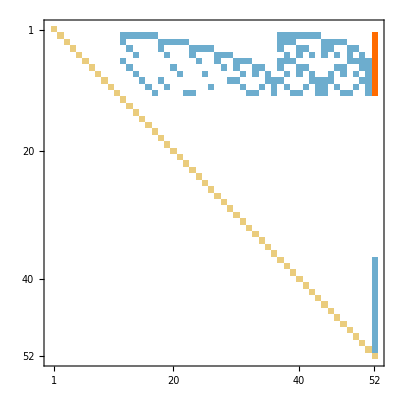
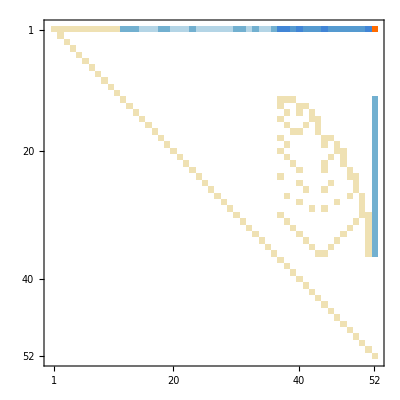
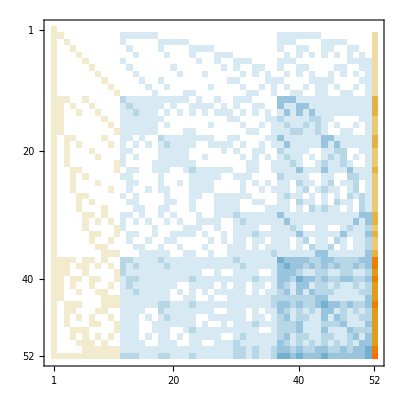
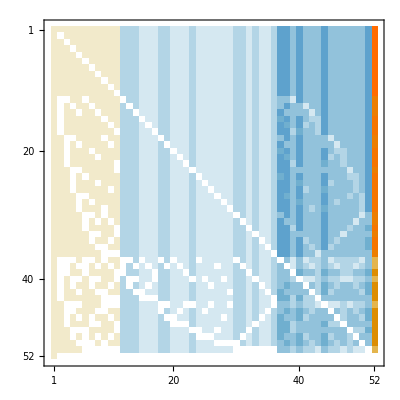
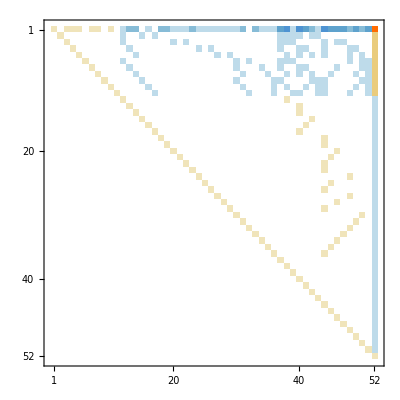
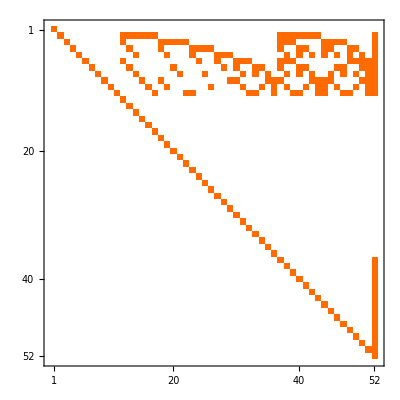
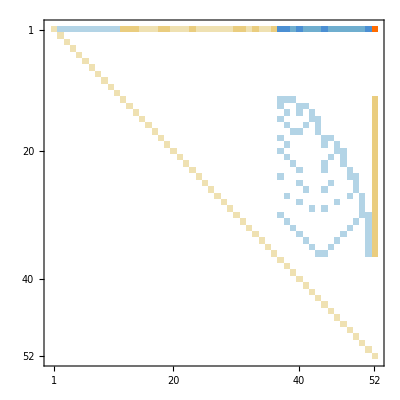
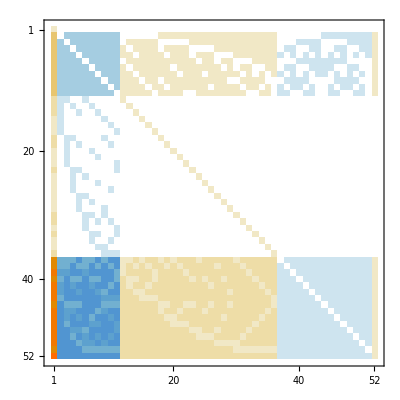
{{-Graphics-C→C,-Graphics-C→E,-Graphics-C→G,-Graphics-C→F,-Graphics-C→T,-Graphics-C→Z},{-Graphics-E→C,-Graphics-E→E,-Graphics-E→G,-Graphics-E→F,-Graphics-E→T,-Graphics-E→Z},{-Graphics-G→C,-Graphics-G→E,-Graphics-G→G,-Graphics-G→F,-Graphics-G→T,-Graphics-G→Z},{-Graphics-F→C,-Graphics-F→E,-Graphics-F→G,-Graphics-F→F,-Graphics-F→T,-Graphics-F→Z},{-Graphics-T→C,-Graphics-T→E,-Graphics-T→G,-Graphics-T→F,-Graphics-T→T,-Graphics-T→Z},{-Graphics-Z→C,-Graphics-Z→E,-Graphics-Z→G,-Graphics-Z→F,-Graphics-Z→T,-Graphics-Z→Z}}

```mathematica
Table[Labeled[MatrixPlot[ConversionMatrix[base1,base2]],base1->base2],{base1,Keys[Bases]},{base2,Keys[Bases]}]
```

```mathematica
Table[Labeled[MatrixPlot[ConversionMatrix[base1,base2]],base1->base2],{base1,{"E","C","Z"}},{base2,{"E","C","Z"}}]//TableForm
```

-Graphics-E→E | -Graphics-E→C | -Graphics-E→Z
-Graphics-C→E | -Graphics-C→C | -Graphics-C→Z
-Graphics-Z→E | -Graphics-Z→C | -Graphics-Z→Z

```mathematica
(allGraphs5[lambdaKey,"colotreejef"]==0//Simplify)/.RepGraph["Z"]
```

30 -Graphics-590481+-Graphics-1312210+-Graphics-437410+-Graphics-16210+-Graphics-5410+-Graphics-610+-Graphics-295240==3 -Graphics-575282+3 -Graphics-544922+-Graphics-529762+3 -Graphics-454162+-Graphics-408962+-Graphics-393922+3 -Graphics-439081+3 -Graphics-189802+-Graphics-63202+-Graphics-21242+3 -Graphics-7282+3 -Graphics-49201+3 -Graphics-147481+3 -Graphics-133401+3 -Graphics-175681+-Graphics-560111+2 -Graphics-514750+-Graphics-499631+-Graphics-492100+2 -Graphics-382810+-Graphics-319540+-Graphics-298571+-Graphics-361660+2 -Graphics-368170+2 -Graphics-297970+-Graphics-361120+-Graphics-360860+-Graphics-324411+-Graphics-303340+2 -Graphics-296330+-Graphics-317380+-Graphics-295600+-Graphics-295371+-Graphics-317140+-Graphics-296080

```mathematica
(allGraphs5[alfaKey,"colotreejef"]//Simplify)/.RepGraph["Z"]
```

6 -Graphics-590481--Graphics-575282--Graphics-544922--Graphics-529762--Graphics-189802--Graphics-147481--Graphics-133401--Graphics-175681--Graphics-560111--Graphics-382810--Graphics-368170--Graphics-360860+-Graphics-1312210

```mathematica
ShowGraph5Least[alfaKey]
```

-Graphics-359771

## En dan

```mathematica
Table[With[{g=allGraphs5[k,"graph"]},If[Mod[VertexCount[g],2]==0,ShowGraph5Least[Convert[k]],ShowGraph5Least[k]]],{k,allGraphs5AtomKeys}]
```

{-Graphics-295240,-Graphics-213,-Graphics-610,-Graphics-1813,-Graphics-295371,-Graphics-5410,-Graphics-295600,-Graphics-16210,-Graphics-296080,-Graphics-296330,-Graphics-48613,-Graphics-297681,-Graphics-297970,-Graphics-298571,-Graphics-7282,-Graphics-145813,-Graphics-302621,-Graphics-303340,-Graphics-304961,-Graphics-21242,-Graphics-437410,-Graphics-317140,-Graphics-317380,-Graphics-319540,-Graphics-49201,-Graphics-324411,-Graphics-63202,-Graphics-1312210,-Graphics-360860,-Graphics-361120,-Graphics-361660,-Graphics-133401,-Graphics-368170,-Graphics-147481,-Graphics-382810,-Graphics-175681,-Graphics-189802,-Graphics-3936613,-Graphics-492081,-Graphics-492100,-Graphics-492161,-Graphics-393922,-Graphics-499631,-Graphics-408962,-Graphics-514750,-Graphics-439081,-Graphics-454162,-Graphics-560111,-Graphics-529762,-Graphics-544922,-Graphics-575282,-Graphics-590481}

```mathematica
sets123=Table[With[{g=allGraphs5[k,"graph"]},If[Mod[VertexCount[g],2]==0,Convert[k],k]],{k,allGraphs5AtomKeys}]
```

{29524,2,6,18,29537,54,29560,162,29608,29633,486,29768,29797,29857,728,1458,30262,30334,30496,2124,4374,31714,31738,31954,4920,32441,6320,13122,36086,36112,36166,13340,36817,14748,38281,17568,18980,39366,49208,49210,49216,39392,49963,40896,51475,43908,45416,56011,52976,54492,57528,59048}

```mathematica
Table[SetsToSymbol[allGraphs5[k,"vertexsets"],"p"],{k,sets123}]
```

{p1x2x3x4x5,p1x2x3x45,p1x2x35x4,p1x2x34x5,p1x2x345,p1x25x3x4,p1x25x34,p1x24x3x5,p1x24x35,p1x245x3,p1x23x4x5,p1x23x45,p1x235x4,p1x234x5,p1x2345,p15x2x3x4,p15x2x34,p15x24x3,p15x23x4,p15x234,p14x2x3x5,p14x2x35,p14x25x3,p14x23x5,p14x235,p145x2x3,p145x23,p13x2x4x5,p13x2x45,p13x25x4,p13x24x5,p13x245,p135x2x4,p135x24,p134x2x5,p134x25,p1345x2,p12x3x4x5,p12x3x45,p12x35x4,p12x34x5,p12x345,p125x3x4,p125x34,p124x3x5,p124x35,p1245x3,p123x4x5,p123x45,p1235x4,p1234x5,p12345}

```mathematica
rep123=First[Solve[Fold[And,Table[SetsToSymbol[allGraphs5[k,"vertexsets"],"p"]==allGraphs5[Convert[k],"colofour"],{k,sets123}]],Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]]];
```

```mathematica
rep123
```

{v1x2x3x4x5→24 p12345+6 p1234x5+6 p1235x4+3 p123x45-p123x4x5+6 p1245x3+3 p124x35-p124x3x5+3 p125x34-p125x3x4+3 p12x345-p12x34x5-p12x35x4-p12x3x45-p12x3x4x5+6 p1345x2+3 p134x25-p134x2x5+3 p135x24-p135x2x4+3 p13x245-p13x24x5-p13x25x4-p13x2x45-p13x2x4x5+3 p145x23-p145x2x3+3 p14x235-p14x23x5-p14x25x3-p14x2x35-p14x2x3x5+3 p15x234-p15x23x4-p15x24x3-p15x2x34-p15x2x3x4+6 p1x2345-p1x234x5-p1x235x4-p1x23x45-p1x23x4x5-p1x245x3-p1x24x35-p1x24x3x5-p1x25x34-p1x25x3x4-p1x2x345-p1x2x34x5-p1x2x35x4-p1x2x3x45+p1x2x3x4x5,v1x2x3x45→p1x2x3x45,v1x2x35x4→p1x2x35x4,v1x2x34x5→p1x2x34x5,v1x2x345→-p12345-p12x345-p1345x2-p1x2345+p1x2x345,v1x25x3x4→p1x25x3x4,v1x25x34→-p12345-p125x34-p134x25-p1x2345+p1x25x34,v1x24x3x5→p1x24x3x5,v1x24x35→-p12345-p124x35-p135x24-p1x2345+p1x24x35,v1x245x3→-p12345-p1245x3-p13x245-p1x2345+p1x245x3,v1x23x4x5→p1x23x4x5,v1x23x45→-p12345-p123x45-p145x23-p1x2345+p1x23x45,v1x235x4→-p12345-p1235x4-p14x235-p1x2345+p1x235x4,v1x234x5→-p12345-p1234x5-p15x234-p1x2345+p1x234x5,v1x2345→p1x2345,v15x2x3x4→p15x2x3x4,v15x2x34→-p12345-p125x34-p1345x2-p15x234+p15x2x34,v15x24x3→-p12345-p1245x3-p135x24-p15x234+p15x24x3,v15x23x4→-p12345-p1235x4-p145x23-p15x234+p15x23x4,v15x234→p15x234,v14x2x3x5→p14x2x3x5,v14x2x35→-p12345-p124x35-p1345x2-p14x235+p14x2x35,v14x25x3→-p12345-p1245x3-p134x25-p14x235+p14x25x3,v14x23x5→-p12345-p1234x5-p145x23-p14x235+p14x23x5,v14x235→p14x235,v145x2x3→-p12345-p1245x3-p1345x2-p145x23+p145x2x3,v145x23→p145x23,v13x2x4x5→p13x2x4x5,v13x2x45→-p12345-p123x45-p1345x2-p13x245+p13x2x45,v13x25x4→-p12345-p1235x4-p134x25-p13x245+p13x25x4,v13x24x5→-p12345-p1234x5-p135x24-p13x245+p13x24x5,v13x245→p13x245,v135x2x4→-p12345-p1235x4-p1345x2-p135x24+p135x2x4,v135x24→p135x24,v134x2x5→-p12345-p1234x5-p1345x2-p134x25+p134x2x5,v134x25→p134x25,v1345x2→p1345x2,v12x3x4x5→p12x3x4x5,v12x3x45→-p12345-p123x45-p1245x3-p12x345+p12x3x45,v12x35x4→-p12345-p1235x4-p124x35-p12x345+p12x35x4,v12x34x5→-p12345-p1234x5-p125x34-p12x345+p12x34x5,v12x345→p12x345,v125x3x4→-p12345-p1235x4-p1245x3-p125x34+p125x3x4,v125x34→p125x34,v124x3x5→-p12345-p1234x5-p1245x3-p124x35+p124x3x5,v124x35→p124x35,v1245x3→p1245x3,v123x4x5→-p12345-p1234x5-p1235x4-p123x45+p123x4x5,v123x45→p123x45,v1235x4→p1235x4,v1234x5→p1234x5,v12345→p12345}

```mathematica
Monitor[Table[allGraphs5[k,"colotreepol"]=Simplify[(allGraphs5[k,"colofour"]/.rep123)],{k,Keys[allGraphs5]}],k]
```

{p1x2x3x4x5,5 p12345+2 p1234x5+2 p1235x4+p123x45-p123x4x5+2 p1245x3+p124x35-p124x3x5+p125x34-p125x3x4+2 p12x345-p12x34x5-p12x35x4-p12x3x45-p12x3x4x5+p1x2x3x4x5,10 p12345+4 p1234x5+4 p1235x4+2 p123x45-p123x4x5+2 p1245x3+p124x35-p124x3x5+p125x34-p125x3x4+2 p12x345-p12x34x5-p12x35x4-p12x3x45-p12x3x4x5+2 p1345x2+p134x25-p134x2x5+p135x24-p135x2x4+2 p13x245-p13x24x5-p13x25x4-p13x2x45-p13x2x4x5+p1x2x3x4x5,1889,-5 p12345-2 p1235x4-2 p124x35-p12x345+p12x35x4-2 p1345x2-p135x24+p135x2x4-p14x235+p14x2x35-2 p1x2345+p1x235x4+p1x24x35+p1x2x345+p1x2x35x4,5 p12345+2 p123x45+2 p1245x3+p12x345-p12x3x45+2 p1345x2+p13x245-p13x2x45+p145x23-p145x2x3+2 p1x2345-p1x23x45-p1x245x3-p1x2x345-p1x2x3x45+p1x2x3x4x5,-5 p12345-2 p123x45-2 p1245x3-p12x345+p12x3x45-2 p1345x2-p13x245+p13x2x45-p145x23+p145x2x3-2 p1x2345+p1x23x45+p1x245x3+p1x2x345+p1x2x3x45}
 |  |  |  |

```mathematica
Bases=Block[{result},
result=Association[];
result["C"]=Association[];
result["C","Colofour"]="colofour";
result["E"]=Association[];
result["E","Colofour"]="colofourrealnull";
result["G"]=Association[];
result["G","Colofour"]="colofourgenerator";
result["F"]=Association[];
result["F","Colofour"]="colofournull";
result["T"]=Association[];
result["T","Colofour"]="colotree";
result["Z"]=Association[];
result["Z","Colofour"]="colotreejef";
result["X"]=Association[];
result["X","Colofour"]="colotreepol";
Table[result[base,"AtomKeys"]=Sort[Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,result[base,"Colofour"]]]]==1&],MyComp[allGraphs5[#1,result[base,"Colofour"]],allGraphs5[#2,result[base,"Colofour"]]]&]
,{base,Keys[result]}];
Table[result[base,"Variables"]=Table[allGraphs5[k,result[base,"Colofour"]],{k,result[base,"AtomKeys"]}]
,{base,Keys[result]}];
result
]
```

<|C→<|Colofour→colofour,AtomKeys→{29524,49207,36085,31711,30253,29767,29605,29551,29533,29527,29525,56011,51475,49963,49216,49210,49208,38281,36817,36166,36112,36086,32441,31954,31738,31714,30496,30334,30262,29857,29797,29768,29633,29608,29560,29537,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{v1x2x3x4x5,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v123x4x5,v124x3x5,v125x3x4,v12x34x5,v12x35x4,v12x3x45,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v145x2x3,v14x23x5,v14x25x3,v14x2x35,v15x23x4,v15x24x3,v15x2x34,v1x234x5,v1x235x4,v1x23x45,v1x245x3,v1x24x35,v1x25x34,v1x2x345,v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345,v12345}|>,E→<|Colofour→colofourrealnull,AtomKeys→{0,39366,13122,4374,1458,486,162,54,18,6,2,52974,43902,40878,39384,39372,39368,17514,14586,13284,13176,13124,5834,4860,4428,4380,1944,1620,1476,666,546,488,218,168,72,26,57528,54492,52976,45416,43908,40896,39392,18980,17568,14748,13340,6320,4920,2124,728,59048},Variables→{n1x2x3x4x5,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n1x2x34x5,n1x2x35x4,n1x2x3x45,n123x4x5,n124x3x5,n125x3x4,n12x34x5,n12x35x4,n12x3x45,n134x2x5,n135x2x4,n13x24x5,n13x25x4,n13x2x45,n145x2x3,n14x23x5,n14x25x3,n14x2x35,n15x23x4,n15x24x3,n15x2x34,n1x234x5,n1x235x4,n1x23x45,n1x245x3,n1x24x35,n1x25x34,n1x2x345,n1234x5,n1235x4,n123x45,n1245x3,n124x35,n125x34,n12x345,n1345x2,n134x25,n135x24,n13x245,n145x23,n14x235,n15x234,n1x2345,n12345}|>,G→<|Colofour→colofourgenerator,AtomKeys→{29524,9841,22963,27337,28795,29281,29443,29497,29515,29521,29523,3037,7573,9085,9832,9838,9840,20767,22231,22882,22936,22962,26607,27094,27310,27334,28552,28714,28786,29191,29251,29280,29415,29440,29488,29511,760,2278,3036,6816,7570,9076,9828,20034,20740,22150,22854,26364,27064,28462,29160,0},Variables→{g1x2x3x4x5,g12x3x4x5,g13x2x4x5,g14x2x3x5,g15x2x3x4,g1x23x4x5,g1x24x3x5,g1x25x3x4,g1x2x34x5,g1x2x35x4,g1x2x3x45,g123x4x5,g124x3x5,g125x3x4,g12x34x5,g12x35x4,g12x3x45,g134x2x5,g135x2x4,g13x24x5,g13x25x4,g13x2x45,g145x2x3,g14x23x5,g14x25x3,g14x2x35,g15x23x4,g15x24x3,g15x2x34,g1x234x5,g1x235x4,g1x23x45,g1x245x3,g1x24x35,g1x25x34,g1x2x345,g1234x5,g1235x4,g123x45,g1245x3,g124x35,g125x34,g12x345,g1345x2,g134x25,g135x24,g13x245,g145x23,g14x235,g15x234,g1x2345,g12345}|>,F→<|Colofour→colofournull,AtomKeys→{0,19683,6561,2187,729,243,81,27,9,3,1,26487,21951,20439,19692,19686,19684,8757,7293,6642,6588,6562,2917,2430,2214,2190,972,810,738,333,273,244,109,84,36,13,28764,27246,26488,22708,21954,20448,19696,9490,8784,7374,6670,3160,2460,1062,364,29524},Variables→{p1x2x3x4x5,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p1x2x34x5,p1x2x35x4,p1x2x3x45,p123x4x5,p124x3x5,p125x3x4,p12x34x5,p12x35x4,p12x3x45,p134x2x5,p135x2x4,p13x24x5,p13x25x4,p13x2x45,p145x2x3,p14x23x5,p14x25x3,p14x2x35,p15x23x4,p15x24x3,p15x2x34,p1x234x5,p1x235x4,p1x23x45,p1x245x3,p1x24x35,p1x25x34,p1x2x345,p1234x5,p1235x4,p123x45,p1245x3,p124x35,p125x34,p12x345,p1345x2,p134x25,p135x24,p13x245,p145x23,p14x235,p15x234,p1x2345,p12345}|>,T→<|Colofour→colotree,AtomKeys→{19936,46180,33130,24384,21420,26821,22287,20721,20029,19969,19940,55252,50718,47694,48460,46942,46184,37548,34620,35434,33916,33158,25868,31224,25168,24414,28308,23770,21510,29128,27610,26852,23072,22318,20812,20060,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{t1x2x3x4x5,t12x3x4x5,t13x2x4x5,t14x2x3x5,t15x2x3x4,t1x23x4x5,t1x24x3x5,t1x25x3x4,t1x2x34x5,t1x2x35x4,t1x2x3x45,t123x4x5,t124x3x5,t125x3x4,t12x34x5,t12x35x4,t12x3x45,t134x2x5,t135x2x4,t13x24x5,t13x25x4,t13x2x45,t145x2x3,t14x23x5,t14x25x3,t14x2x35,t15x23x4,t15x24x3,t15x2x34,t1x234x5,t1x235x4,t1x23x45,t1x245x3,t1x24x35,t1x25x34,t1x2x345,t1234x5,t1235x4,t123x45,t1245x3,t124x35,t125x34,t12x345,t1345x2,t134x25,t135x24,t13x245,t145x23,t14x235,t15x234,t1x2345,t12345}|>,Z→<|Colofour→colotreejef,AtomKeys→{29524,39366,13122,4374,1458,486,162,54,18,6,2,56011,51475,49963,49216,49210,49208,38281,36817,36166,36112,36086,32441,31954,31738,31714,30496,30334,30262,29857,29797,29768,29633,29608,29560,29537,57528,54492,52976,45416,43908,40896,39392,18980,17568,14748,13340,6320,4920,2124,728,59048},Variables→{z1x2x3x4x5,z12x3x4x5,z13x2x4x5,z14x2x3x5,z15x2x3x4,z1x23x4x5,z1x24x3x5,z1x25x3x4,z1x2x34x5,z1x2x35x4,z1x2x3x45,z123x4x5,z124x3x5,z125x3x4,z12x34x5,z12x35x4,z12x3x45,z134x2x5,z135x2x4,z13x24x5,z13x25x4,z13x2x45,z145x2x3,z14x23x5,z14x25x3,z14x2x35,z15x23x4,z15x24x3,z15x2x34,z1x234x5,z1x235x4,z1x23x45,z1x245x3,z1x24x35,z1x25x34,z1x2x345,z1234x5,z1235x4,z123x45,z1245x3,z124x35,z125x34,z12x345,z1345x2,z134x25,z135x24,z13x245,z145x23,z14x235,z15x234,z1x2345,z12345}|>,X→<|Colofour→colotreepol,AtomKeys→{0,49207,36085,31711,30253,29767,29605,29551,29533,29527,29525,52974,43902,40878,39384,39372,39368,17514,14586,13284,13176,13124,5834,4860,4428,4380,1944,1620,1476,666,546,488,218,168,72,26,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{p1x2x3x4x5,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p1x2x34x5,p1x2x35x4,p1x2x3x45,p123x4x5,p124x3x5,p125x3x4,p12x34x5,p12x35x4,p12x3x45,p134x2x5,p135x2x4,p13x24x5,p13x25x4,p13x2x45,p145x2x3,p14x23x5,p14x25x3,p14x2x35,p15x23x4,p15x24x3,p15x2x34,p1x234x5,p1x235x4,p1x23x45,p1x245x3,p1x24x35,p1x25x34,p1x2x345,p1234x5,p1235x4,p123x45,p1245x3,p124x35,p125x34,p12x345,p1345x2,p134x25,p135x24,p13x245,p145x23,p14x235,p15x234,p1x2345,p12345}|>|>

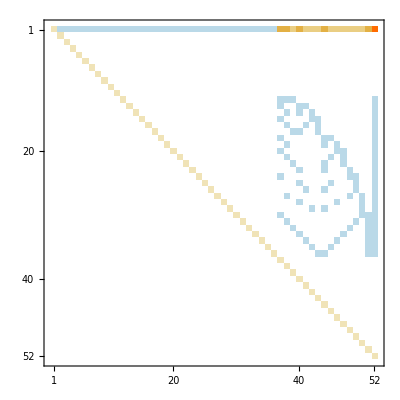
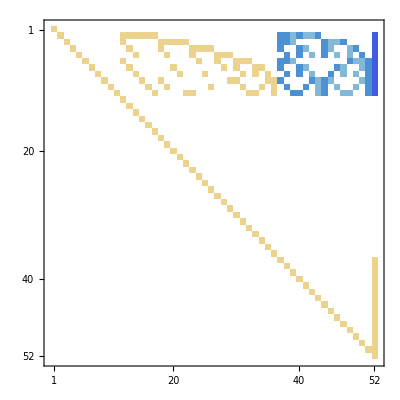
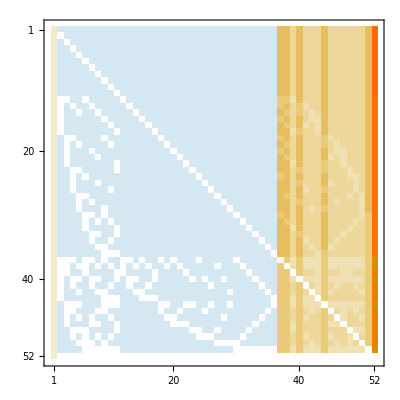
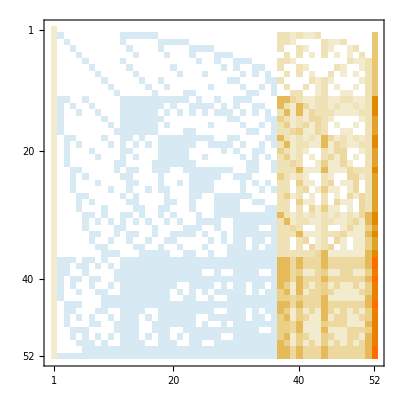
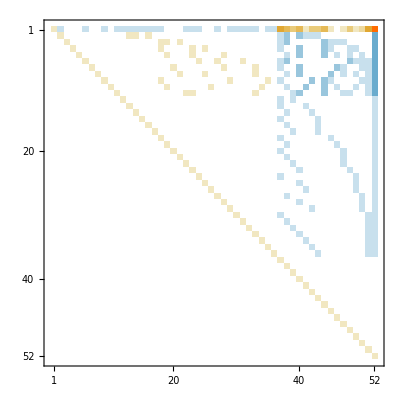
{{-Graphics-C→C,-Graphics-C→E,-Graphics-C→G,-Graphics-C→F,-Graphics-C→T,-Graphics-C→Z,-Graphics-C→X},{-Graphics-E→C,-Graphics-E→E,-Graphics-E→G,-Graphics-E→F,-Graphics-E→T,-Graphics-E→Z,-Graphics-E→X},{-Graphics-G→C,-Graphics-G→E,-Graphics-G→G,-Graphics-G→F,-Graphics-G→T,-Graphics-G→Z,-Graphics-G→X},{-Graphics-F→C,-Graphics-F→E,-Graphics-F→G,-Graphics-F→F,-Graphics-F→T,-Graphics-F→Z,-Graphics-F→X},{-Graphics-T→C,-Graphics-T→E,-Graphics-T→G,-Graphics-T→F,-Graphics-T→T,-Graphics-T→Z,-Graphics-T→X},{-Graphics-Z→C,-Graphics-Z→E,-Graphics-Z→G,-Graphics-Z→F,-Graphics-Z→T,-Graphics-Z→Z,-Graphics-Z→X},{-Graphics-X→C,-Graphics-X→E,-Graphics-X→G,-Graphics-X→F,-Graphics-X→T,-Graphics-X→Z,-Graphics-X→X}}

```mathematica
Table[Labeled[MatrixPlot[ConversionMatrix[base1,base2]],base1->base2],{base1,Keys[Bases]},{base2,Keys[Bases]}]
```

```mathematica
Table[Labeled[MatrixPlot[ConversionMatrix[base1,base2]],base1->base2],{base1,{"E","C","Z","X"}},{base2,{"E","C","Z","X"}}]//TableForm
```

-Graphics-E→E | -Graphics-E→C | -Graphics-E→Z | -Graphics-E→X
-Graphics-C→E | -Graphics-C→C | -Graphics-C→Z | -Graphics-C→X
-Graphics-Z→E | -Graphics-Z→C | -Graphics-Z→Z | -Graphics-Z→X
-Graphics-X→E | -Graphics-X→C | -Graphics-X→Z | -Graphics-X→X

```mathematica
Table[Labeled[MatrixPlot[Inverse[ConversionMatrix[base1,base2]]],base1->base2],{base1,{"E","C","Z","X"}},{base2,{"E","C","Z","X"}}]//TableForm
```

-Graphics-E→E | -Graphics-E→C | -Graphics-E→Z | -Graphics-E→X
-Graphics-C→E | -Graphics-C→C | -Graphics-C→Z | -Graphics-C→X
-Graphics-Z→E | -Graphics-Z→C | -Graphics-Z→Z | -Graphics-Z→X
-Graphics-X→E | -Graphics-X→C | -Graphics-X→Z | -Graphics-X→X

```mathematica
(allGraphs5[lambdaKey,"colotreepol"]==0//Simplify)/.RepGraph["X"]
```

19 -Graphics-590481+5 -Graphics-582881+5 -Graphics-567701+3 -Graphics-560121+5 -Graphics-522321+3 -Graphics-499721+3 -Graphics-492201+-Graphics-514780+5 -Graphics-390141+3 -Graphics-326841+3 -Graphics-305861+5 -Graphics-298881+-Graphics-319840+-Graphics-368980+-Graphics-361940+-Graphics-383080+-Graphics-034==-Graphics-529745+-Graphics-439024+-Graphics-393845+-Graphics-408785+-Graphics-393724+-Graphics-393685+-Graphics-175144+-Graphics-48604+-Graphics-6665+-Graphics-145864+-Graphics-19445+-Graphics-5464+-Graphics-131244+-Graphics-4885+-Graphics-58345+-Graphics-16204+-Graphics-2184+-Graphics-14765+-Graphics-724+-Graphics-265+-Graphics-492070+-Graphics-297670+-Graphics-295330+-Graphics-302530+-Graphics-295250

```mathematica
(allGraphs5[alfaKey,"colotreepol"]//Simplify)/.RepGraph["X"]
```

-2 -Graphics-590481--Graphics-582881--Graphics-567701--Graphics-368980-2 -Graphics-361940--Graphics-383080+-Graphics-132842+-Graphics-131762+-Graphics-360850

```mathematica
(allGraphs5[alfaKey,"colotreejef"]//Simplify)/.RepGraph["Z"]
```

6 -Graphics-590481--Graphics-575282--Graphics-544922--Graphics-529762--Graphics-189802--Graphics-147481--Graphics-133401--Graphics-175681--Graphics-560111--Graphics-382810--Graphics-368170--Graphics-360860+-Graphics-1312210

```mathematica
ShowGraph5Least[alfaKey]
```

-Graphics-359771

```mathematica
MatrixForm[ConversionMatrix["X","C"]]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[ConversionMatrix["Z","C"]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[ConversionMatrix["X","C"]-IdentityMatrix[52]+ConversionMatrix["Z","C"]]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixPlot[ConversionMatrix["X","C"]-IdentityMatrix[52]+ConversionMatrix["Z","C"]]
```

-Graphics-

```mathematica
MatrixPlot[ConversionMatrix["E","C"]]
```

-Graphics-

```mathematica
(ConversionMatrix["X","C"]-IdentityMatrix[52]+ConversionMatrix["Z","C"])==ConversionMatrix["E","C"]
```

True

```mathematica
(ConversionMatrix["X","C"]-IdentityMatrix[52]+ConversionMatrix["Z","C"])-ConversionMatrix["C","E"]
```

{{0,2,2,2,2,2,2,2,2,2,2,-1,-1,-1,0,0,0,-1,-1,0,0,0,-1,0,0,0,0,0,0,-1,-1,0,-1,0,0,-1,7,7,3,7,3,3,3,7,3,3,3,3,3,3,7,-23},{0,0,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,-1,0,0,-1,0,0,0,0,0,0,0,0,7},{0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,0,0,0,0,-1,0,0,-1,0,0,0,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,2,2,2,2,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,-1,0,0,0,0,-1,0,0,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,0,2,0,0,0,2,2,2,0,0,0,0,0,0,0,0,-1,0,-1,0,0,0,-1,0,0,0,0,0,-1,0,7},{0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,2,2,2,0,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,-1,0,0,-1,7},{0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,2,0,0,0,0,0,0,0,2,0,2,0,0,2,2,0,0,-1,0,0,-1,0,0,0,0,0,-1,0,0,0,0,-1,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,2,0,2,0,2,0,0,-1,0,-1,0,0,0,0,-1,0,0,0,0,0,-1,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,2,2,-1,0,0,0,0,-1,0,-1,0,0,0,0,0,0,-1,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0,0,0,0,2,0,0,0,0,2,0,0,2,0,2,0,-1,0,0,-1,0,0,-1,0,0,0,0,0,0,-1,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,2,0,0,0,0,0,0,0,0,2,2,0,0,2,0,0,-1,-1,0,0,0,-1,0,0,0,0,0,0,-1,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,2,0,0,0,0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,2,0,0,0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,2,0,0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,2,0,0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,2,0,0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,2,2,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,2,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,2,2,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,2,0,2,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,2,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,2,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,2,2,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,0,2,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0,0,2,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,2,0,2,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,2,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,0,0,0,0,0,2,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,2,2,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,2,0,2,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,2,0,0,2,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,2,0,0,0,2,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,2,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0,0,0,2,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,2,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

## En dan

```mathematica
letter="A";
```

```mathematica
Table[With[{g=allGraphs5[k,"graph"]},If[VertexCount[g]==4,ShowGraph5Least[Convert[k]],ShowGraph5Least[k]]],{k,allGraphs5AtomKeys}]
```

{-Graphics-295240,-Graphics-213,-Graphics-610,-Graphics-1813,-Graphics-295371,-Graphics-5410,-Graphics-295600,-Graphics-16210,-Graphics-296080,-Graphics-296330,-Graphics-48613,-Graphics-297681,-Graphics-297970,-Graphics-298571,-Graphics-298881,-Graphics-145813,-Graphics-302621,-Graphics-303340,-Graphics-304961,-Graphics-305861,-Graphics-437410,-Graphics-317140,-Graphics-317380,-Graphics-319540,-Graphics-319840,-Graphics-324411,-Graphics-326841,-Graphics-1312210,-Graphics-360860,-Graphics-361120,-Graphics-361660,-Graphics-361940,-Graphics-368170,-Graphics-368980,-Graphics-382810,-Graphics-383080,-Graphics-390141,-Graphics-3936613,-Graphics-492081,-Graphics-492100,-Graphics-492161,-Graphics-492201,-Graphics-499631,-Graphics-499721,-Graphics-514750,-Graphics-514780,-Graphics-522321,-Graphics-560111,-Graphics-560121,-Graphics-567701,-Graphics-582881,-Graphics-590481}

```mathematica
sets123=Table[With[{g=allGraphs5[k,"graph"]},If[VertexCount[g]==4,Convert[k],k]],{k,allGraphs5AtomKeys}]
```

{29524,2,6,18,29537,54,29560,162,29608,29633,486,29768,29797,29857,29888,1458,30262,30334,30496,30586,4374,31714,31738,31954,31984,32441,32684,13122,36086,36112,36166,36194,36817,36898,38281,38308,39014,39366,49208,49210,49216,49220,49963,49972,51475,51478,52232,56011,56012,56770,58288,59048}

```mathematica
Table[SetsToSymbol[allGraphs5[k,"vertexsets"],letter],{k,sets123}]
```

{A1x2x3x4x5,A1x2x3x45,A1x2x35x4,A1x2x34x5,A1x2x345,A1x25x3x4,A1x25x34,A1x24x3x5,A1x24x35,A1x245x3,A1x23x4x5,A1x23x45,A1x235x4,A1x234x5,A1x2345,A15x2x3x4,A15x2x34,A15x24x3,A15x23x4,A15x234,A14x2x3x5,A14x2x35,A14x25x3,A14x23x5,A14x235,A145x2x3,A145x23,A13x2x4x5,A13x2x45,A13x25x4,A13x24x5,A13x245,A135x2x4,A135x24,A134x2x5,A134x25,A1345x2,A12x3x4x5,A12x3x45,A12x35x4,A12x34x5,A12x345,A125x3x4,A125x34,A124x3x5,A124x35,A1245x3,A123x4x5,A123x45,A1235x4,A1234x5,A12345}

```mathematica
rep123=First[Solve[Fold[And,Table[SetsToSymbol[allGraphs5[k,"vertexsets"],letter]==allGraphs5[Convert[k],"colofour"],{k,sets123}]],Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]]];
```

```mathematica
rep123
```

{v1x2x3x4x5→-36 A12345+6 A1234x5+6 A1235x4+3 A123x45-A123x4x5+6 A1245x3+3 A124x35-A124x3x5+3 A125x34-A125x3x4+3 A12x345-A12x34x5-A12x35x4-A12x3x45-A12x3x4x5+6 A1345x2+3 A134x25-A134x2x5+3 A135x24-A135x2x4+3 A13x245-A13x24x5-A13x25x4-A13x2x45-A13x2x4x5+3 A145x23-A145x2x3+3 A14x235-A14x23x5-A14x25x3-A14x2x35-A14x2x3x5+3 A15x234-A15x23x4-A15x24x3-A15x2x34-A15x2x3x4+6 A1x2345-A1x234x5-A1x235x4-A1x23x45-A1x23x4x5-A1x245x3-A1x24x35-A1x24x3x5-A1x25x34-A1x25x3x4-A1x2x345-A1x2x34x5-A1x2x35x4-A1x2x3x45+A1x2x3x4x5,v1x2x3x45→A1x2x3x45,v1x2x35x4→A1x2x35x4,v1x2x34x5→A1x2x34x5,v1x2x345→2 A12345-A12x345-A1345x2-A1x2345+A1x2x345,v1x25x3x4→A1x25x3x4,v1x25x34→2 A12345-A125x34-A134x25-A1x2345+A1x25x34,v1x24x3x5→A1x24x3x5,v1x24x35→2 A12345-A124x35-A135x24-A1x2345+A1x24x35,v1x245x3→2 A12345-A1245x3-A13x245-A1x2345+A1x245x3,v1x23x4x5→A1x23x4x5,v1x23x45→2 A12345-A123x45-A145x23-A1x2345+A1x23x45,v1x235x4→2 A12345-A1235x4-A14x235-A1x2345+A1x235x4,v1x234x5→2 A12345-A1234x5-A15x234-A1x2345+A1x234x5,v1x2345→-A12345+A1x2345,v15x2x3x4→A15x2x3x4,v15x2x34→2 A12345-A125x34-A1345x2-A15x234+A15x2x34,v15x24x3→2 A12345-A1245x3-A135x24-A15x234+A15x24x3,v15x23x4→2 A12345-A1235x4-A145x23-A15x234+A15x23x4,v15x234→-A12345+A15x234,v14x2x3x5→A14x2x3x5,v14x2x35→2 A12345-A124x35-A1345x2-A14x235+A14x2x35,v14x25x3→2 A12345-A1245x3-A134x25-A14x235+A14x25x3,v14x23x5→2 A12345-A1234x5-A145x23-A14x235+A14x23x5,v14x235→-A12345+A14x235,v145x2x3→2 A12345-A1245x3-A1345x2-A145x23+A145x2x3,v145x23→-A12345+A145x23,v13x2x4x5→A13x2x4x5,v13x2x45→2 A12345-A123x45-A1345x2-A13x245+A13x2x45,v13x25x4→2 A12345-A1235x4-A134x25-A13x245+A13x25x4,v13x24x5→2 A12345-A1234x5-A135x24-A13x245+A13x24x5,v13x245→-A12345+A13x245,v135x2x4→2 A12345-A1235x4-A1345x2-A135x24+A135x2x4,v135x24→-A12345+A135x24,v134x2x5→2 A12345-A1234x5-A1345x2-A134x25+A134x2x5,v134x25→-A12345+A134x25,v1345x2→-A12345+A1345x2,v12x3x4x5→A12x3x4x5,v12x3x45→2 A12345-A123x45-A1245x3-A12x345+A12x3x45,v12x35x4→2 A12345-A1235x4-A124x35-A12x345+A12x35x4,v12x34x5→2 A12345-A1234x5-A125x34-A12x345+A12x34x5,v12x345→-A12345+A12x345,v125x3x4→2 A12345-A1235x4-A1245x3-A125x34+A125x3x4,v125x34→-A12345+A125x34,v124x3x5→2 A12345-A1234x5-A1245x3-A124x35+A124x3x5,v124x35→-A12345+A124x35,v1245x3→-A12345+A1245x3,v123x4x5→2 A12345-A1234x5-A1235x4-A123x45+A123x4x5,v123x45→-A12345+A123x45,v1235x4→-A12345+A1235x4,v1234x5→-A12345+A1234x5,v12345→A12345}

```mathematica
Monitor[Table[allGraphs5[k,letter]=Simplify[(allGraphs5[k,"colofour"]/.rep123)],{k,Keys[allGraphs5]}],k]
```

{A1x2x3x4x5,-6 A12345+2 A1234x5+2 A1235x4+A123x45-A123x4x5+2 A1245x3+A124x35-A124x3x5+A125x34-A125x3x4+2 A12x345-A12x34x5-A12x35x4-A12x3x45-A12x3x4x5+A1x2x3x4x5,-12 A12345+4 A1234x5+4 A1235x4+2 A123x45-A123x4x5+2 A1245x3+A124x35-A124x3x5+A125x34-A125x3x4+2 A12x345-A12x34x5-A12x35x4-A12x3x45-A12x3x4x5+2 A1345x2+A134x25-A134x2x5+A135x24-A135x2x4+2 A13x245-A13x24x5-A13x25x4-A13x2x45-A13x2x4x5+A1x2x3x4x5,1889,6 A12345-2 A1235x4-2 A124x35-A12x345+A12x35x4-2 A1345x2-A135x24+A135x2x4-A14x235+A14x2x35-2 A1x2345+A1x235x4+A1x24x35+A1x2x345+A1x2x35x4,-6 A12345+2 A123x45+2 A1245x3+A12x345-A12x3x45+2 A1345x2+A13x245-A13x2x45+A145x23-A145x2x3+2 A1x2345-A1x23x45-A1x245x3-A1x2x345-A1x2x3x45+A1x2x3x4x5,6 A12345-2 A123x45-2 A1245x3-A12x345+A12x3x45-2 A1345x2-A13x245+A13x2x45-A145x23+A145x2x3-2 A1x2345+A1x23x45+A1x245x3+A1x2x345+A1x2x3x45}
 |  |  |  |

```mathematica
Bases=Block[{result},
result=Association[];
result["C"]=Association[];
result["C","Colofour"]="colofour";
result["E"]=Association[];
result["E","Colofour"]="colofourrealnull";
result["G"]=Association[];
result["G","Colofour"]="colofourgenerator";
result["F"]=Association[];
result["F","Colofour"]="colofournull";
result["T"]=Association[];
result["T","Colofour"]="colotree";
result["Z"]=Association[];
result["Z","Colofour"]="colotreejef";
result["X"]=Association[];
result["X","Colofour"]="colotreepol";
result[letter]=Association[];
result[letter,"Colofour"]=letter;
Table[result[base,"AtomKeys"]=Sort[Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,result[base,"Colofour"]]]]==1&],MyComp[allGraphs5[#1,result[base,"Colofour"]],allGraphs5[#2,result[base,"Colofour"]]]&]
,{base,Keys[result]}];
Table[result[base,"Variables"]=Table[allGraphs5[k,result[base,"Colofour"]],{k,result[base,"AtomKeys"]}]
,{base,Keys[result]}];
result
]
```

<|C→<|Colofour→colofour,AtomKeys→{29524,49207,36085,31711,30253,29767,29605,29551,29533,29527,29525,56011,51475,49963,49216,49210,49208,38281,36817,36166,36112,36086,32441,31954,31738,31714,30496,30334,30262,29857,29797,29768,29633,29608,29560,29537,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{v1x2x3x4x5,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v123x4x5,v124x3x5,v125x3x4,v12x34x5,v12x35x4,v12x3x45,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v145x2x3,v14x23x5,v14x25x3,v14x2x35,v15x23x4,v15x24x3,v15x2x34,v1x234x5,v1x235x4,v1x23x45,v1x245x3,v1x24x35,v1x25x34,v1x2x345,v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345,v12345}|>,E→<|Colofour→colofourrealnull,AtomKeys→{0,39366,13122,4374,1458,486,162,54,18,6,2,52974,43902,40878,39384,39372,39368,17514,14586,13284,13176,13124,5834,4860,4428,4380,1944,1620,1476,666,546,488,218,168,72,26,57528,54492,52976,45416,43908,40896,39392,18980,17568,14748,13340,6320,4920,2124,728,59048},Variables→{n1x2x3x4x5,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n1x2x34x5,n1x2x35x4,n1x2x3x45,n123x4x5,n124x3x5,n125x3x4,n12x34x5,n12x35x4,n12x3x45,n134x2x5,n135x2x4,n13x24x5,n13x25x4,n13x2x45,n145x2x3,n14x23x5,n14x25x3,n14x2x35,n15x23x4,n15x24x3,n15x2x34,n1x234x5,n1x235x4,n1x23x45,n1x245x3,n1x24x35,n1x25x34,n1x2x345,n1234x5,n1235x4,n123x45,n1245x3,n124x35,n125x34,n12x345,n1345x2,n134x25,n135x24,n13x245,n145x23,n14x235,n15x234,n1x2345,n12345}|>,G→<|Colofour→colofourgenerator,AtomKeys→{29524,9841,22963,27337,28795,29281,29443,29497,29515,29521,29523,3037,7573,9085,9832,9838,9840,20767,22231,22882,22936,22962,26607,27094,27310,27334,28552,28714,28786,29191,29251,29280,29415,29440,29488,29511,760,2278,3036,6816,7570,9076,9828,20034,20740,22150,22854,26364,27064,28462,29160,0},Variables→{g1x2x3x4x5,g12x3x4x5,g13x2x4x5,g14x2x3x5,g15x2x3x4,g1x23x4x5,g1x24x3x5,g1x25x3x4,g1x2x34x5,g1x2x35x4,g1x2x3x45,g123x4x5,g124x3x5,g125x3x4,g12x34x5,g12x35x4,g12x3x45,g134x2x5,g135x2x4,g13x24x5,g13x25x4,g13x2x45,g145x2x3,g14x23x5,g14x25x3,g14x2x35,g15x23x4,g15x24x3,g15x2x34,g1x234x5,g1x235x4,g1x23x45,g1x245x3,g1x24x35,g1x25x34,g1x2x345,g1234x5,g1235x4,g123x45,g1245x3,g124x35,g125x34,g12x345,g1345x2,g134x25,g135x24,g13x245,g145x23,g14x235,g15x234,g1x2345,g12345}|>,F→<|Colofour→colofournull,AtomKeys→{0,19683,6561,2187,729,243,81,27,9,3,1,26487,21951,20439,19692,19686,19684,8757,7293,6642,6588,6562,2917,2430,2214,2190,972,810,738,333,273,244,109,84,36,13,28764,27246,26488,22708,21954,20448,19696,9490,8784,7374,6670,3160,2460,1062,364,29524},Variables→{p1x2x3x4x5,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p1x2x34x5,p1x2x35x4,p1x2x3x45,p123x4x5,p124x3x5,p125x3x4,p12x34x5,p12x35x4,p12x3x45,p134x2x5,p135x2x4,p13x24x5,p13x25x4,p13x2x45,p145x2x3,p14x23x5,p14x25x3,p14x2x35,p15x23x4,p15x24x3,p15x2x34,p1x234x5,p1x235x4,p1x23x45,p1x245x3,p1x24x35,p1x25x34,p1x2x345,p1234x5,p1235x4,p123x45,p1245x3,p124x35,p125x34,p12x345,p1345x2,p134x25,p135x24,p13x245,p145x23,p14x235,p15x234,p1x2345,p12345}|>,T→<|Colofour→colotree,AtomKeys→{19936,46180,33130,24384,21420,26821,22287,20721,20029,19969,19940,55252,50718,47694,48460,46942,46184,37548,34620,35434,33916,33158,25868,31224,25168,24414,28308,23770,21510,29128,27610,26852,23072,22318,20812,20060,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{t1x2x3x4x5,t12x3x4x5,t13x2x4x5,t14x2x3x5,t15x2x3x4,t1x23x4x5,t1x24x3x5,t1x25x3x4,t1x2x34x5,t1x2x35x4,t1x2x3x45,t123x4x5,t124x3x5,t125x3x4,t12x34x5,t12x35x4,t12x3x45,t134x2x5,t135x2x4,t13x24x5,t13x25x4,t13x2x45,t145x2x3,t14x23x5,t14x25x3,t14x2x35,t15x23x4,t15x24x3,t15x2x34,t1x234x5,t1x235x4,t1x23x45,t1x245x3,t1x24x35,t1x25x34,t1x2x345,t1234x5,t1235x4,t123x45,t1245x3,t124x35,t125x34,t12x345,t1345x2,t134x25,t135x24,t13x245,t145x23,t14x235,t15x234,t1x2345,t12345}|>,Z→<|Colofour→colotreejef,AtomKeys→{29524,39366,13122,4374,1458,486,162,54,18,6,2,56011,51475,49963,49216,49210,49208,38281,36817,36166,36112,36086,32441,31954,31738,31714,30496,30334,30262,29857,29797,29768,29633,29608,29560,29537,57528,54492,52976,45416,43908,40896,39392,18980,17568,14748,13340,6320,4920,2124,728,59048},Variables→{z1x2x3x4x5,z12x3x4x5,z13x2x4x5,z14x2x3x5,z15x2x3x4,z1x23x4x5,z1x24x3x5,z1x25x3x4,z1x2x34x5,z1x2x35x4,z1x2x3x45,z123x4x5,z124x3x5,z125x3x4,z12x34x5,z12x35x4,z12x3x45,z134x2x5,z135x2x4,z13x24x5,z13x25x4,z13x2x45,z145x2x3,z14x23x5,z14x25x3,z14x2x35,z15x23x4,z15x24x3,z15x2x34,z1x234x5,z1x235x4,z1x23x45,z1x245x3,z1x24x35,z1x25x34,z1x2x345,z1234x5,z1235x4,z123x45,z1245x3,z124x35,z125x34,z12x345,z1345x2,z134x25,z135x24,z13x245,z145x23,z14x235,z15x234,z1x2345,z12345}|>,X→<|Colofour→colotreepol,AtomKeys→{0,49207,36085,31711,30253,29767,29605,29551,29533,29527,29525,52974,43902,40878,39384,39372,39368,17514,14586,13284,13176,13124,5834,4860,4428,4380,1944,1620,1476,666,546,488,218,168,72,26,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{p1x2x3x4x5,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p1x2x34x5,p1x2x35x4,p1x2x3x45,p123x4x5,p124x3x5,p125x3x4,p12x34x5,p12x35x4,p12x3x45,p134x2x5,p135x2x4,p13x24x5,p13x25x4,p13x2x45,p145x2x3,p14x23x5,p14x25x3,p14x2x35,p15x23x4,p15x24x3,p15x2x34,p1x234x5,p1x235x4,p1x23x45,p1x245x3,p1x24x35,p1x25x34,p1x2x345,p1234x5,p1235x4,p123x45,p1245x3,p124x35,p125x34,p12x345,p1345x2,p134x25,p135x24,p13x245,p145x23,p14x235,p15x234,p1x2345,p12345}|>,A→<|Colofour→A,AtomKeys→{0,49207,36085,31711,30253,29767,29605,29551,29533,29527,29525,52974,43902,40878,39384,39372,39368,17514,14586,13284,13176,13124,5834,4860,4428,4380,1944,1620,1476,666,546,488,218,168,72,26,57528,54492,52976,45416,43908,40896,39392,18980,17568,14748,13340,6320,4920,2124,728,59048},Variables→{A1x2x3x4x5,A12x3x4x5,A13x2x4x5,A14x2x3x5,A15x2x3x4,A1x23x4x5,A1x24x3x5,A1x25x3x4,A1x2x34x5,A1x2x35x4,A1x2x3x45,A123x4x5,A124x3x5,A125x3x4,A12x34x5,A12x35x4,A12x3x45,A134x2x5,A135x2x4,A13x24x5,A13x25x4,A13x2x45,A145x2x3,A14x23x5,A14x25x3,A14x2x35,A15x23x4,A15x24x3,A15x2x34,A1x234x5,A1x235x4,A1x23x45,A1x245x3,A1x24x35,A1x25x34,A1x2x345,A1234x5,A1235x4,A123x45,A1245x3,A124x35,A125x34,A12x345,A1345x2,A134x25,A135x24,A13x245,A145x23,A14x235,A15x234,A1x2345,A12345}|>|>

```mathematica
Table[Labeled[MatrixPlot[ConversionMatrix[base1,base2]],base1->base2],{base1,Keys[Bases]},{base2,Keys[Bases]}]
```

{{-Graphics-C→C,-Graphics-C→E,-Graphics-C→G,-Graphics-C→F,-Graphics-C→T,-Graphics-C→Z,-Graphics-C→X,-Graphics-C→A},{-Graphics-E→C,-Graphics-E→E,-Graphics-E→G,-Graphics-E→F,-Graphics-E→T,-Graphics-E→Z,-Graphics-E→X,-Graphics-E→A},{-Graphics-G→C,-Graphics-G→E,-Graphics-G→G,-Graphics-G→F,-Graphics-G→T,-Graphics-G→Z,-Graphics-G→X,-Graphics-G→A},{-Graphics-F→C,-Graphics-F→E,-Graphics-F→G,-Graphics-F→F,-Graphics-F→T,-Graphics-F→Z,-Graphics-F→X,-Graphics-F→A},{-Graphics-T→C,-Graphics-T→E,-Graphics-T→G,-Graphics-T→F,-Graphics-T→T,-Graphics-T→Z,-Graphics-T→X,-Graphics-T→A},{-Graphics-Z→C,-Graphics-Z→E,-Graphics-Z→G,-Graphics-Z→F,-Graphics-Z→T,-Graphics-Z→Z,-Graphics-Z→X,-Graphics-Z→A},{-Graphics-X→C,-Graphics-X→E,-Graphics-X→G,-Graphics-X→F,-Graphics-X→T,-Graphics-X→Z,-Graphics-X→X,-Graphics-X→A},{-Graphics-A→C,-Graphics-A→E,-Graphics-A→G,-Graphics-A→F,-Graphics-A→T,-Graphics-A→Z,-Graphics-A→X,-Graphics-A→A}}

```mathematica
Table[VertexCount[allGraphs5[k,"graph"]],{k,allGraphs5AtomKeys}]//Sort
```

{1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,5}

```mathematica
Table[Labeled[MatrixPlot[ConversionMatrix[base1,base2]],base1->base2],{base1,{"E","C","Z","X",letter}},{base2,{"E","C","Z","X",letter}}]//TableForm
```

-Graphics-E→E | -Graphics-E→C | -Graphics-E→Z | -Graphics-E→X | -Graphics-E→A
-Graphics-C→E | -Graphics-C→C | -Graphics-C→Z | -Graphics-C→X | -Graphics-C→A
-Graphics-Z→E | -Graphics-Z→C | -Graphics-Z→Z | -Graphics-Z→X | -Graphics-Z→A
-Graphics-X→E | -Graphics-X→C | -Graphics-X→Z | -Graphics-X→X | -Graphics-X→A
-Graphics-A→E | -Graphics-A→C | -Graphics-A→Z | -Graphics-A→X | -Graphics-A→A

```mathematica
(allGraphs5[lambdaKey,letter]==0//Simplify)/.RepGraph[letter]
```

26 -Graphics-590481+-Graphics-529745+-Graphics-439024+-Graphics-393845+-Graphics-408785+-Graphics-393724+-Graphics-393685+-Graphics-175144+-Graphics-48604+-Graphics-6665+-Graphics-145864+-Graphics-19445+-Graphics-5464+-Graphics-131244+-Graphics-4885+-Graphics-58345+-Graphics-16204+-Graphics-2184+-Graphics-14765+-Graphics-724+-Graphics-265+-Graphics-492070+-Graphics-297670+-Graphics-295330+-Graphics-302530+-Graphics-295250==5 -Graphics-575282+5 -Graphics-544922+3 -Graphics-529762+5 -Graphics-454162+3 -Graphics-408962+3 -Graphics-393922+-Graphics-439081+5 -Graphics-189802+3 -Graphics-63202+3 -Graphics-21242+5 -Graphics-7282+-Graphics-49201+-Graphics-147481+-Graphics-133401+-Graphics-175681+-Graphics-034

```mathematica
(allGraphs5[alfaKey,letter]//Simplify)/.RepGraph[letter]
```

4 -Graphics-590481--Graphics-575282--Graphics-544922--Graphics-147481-2 -Graphics-133401--Graphics-175681+-Graphics-132842+-Graphics-131762+-Graphics-360850

```mathematica
(allGraphs5[alfa1Key,letter]//Simplify)/.RepGraph[letter]
```

2 -Graphics-590481--Graphics-575282--Graphics-147481--Graphics-133401+-Graphics-132842

```mathematica
ShowGraph5Least[alfa1Key]
```

-Graphics-361660

```mathematica
MatrixPlot[ConversionMatrix[letter,"C"]-IdentityMatrix[52]+ConversionMatrix["Z","C"]]
```

-Graphics-

```mathematica
MatrixPlot[ConversionMatrix["E","C"]]
```

-Graphics-

```mathematica
(ConversionMatrix["X","C"]-IdentityMatrix[52]+ConversionMatrix["Z","C"])==ConversionMatrix["E","C"]
```

True